```mathematica
description="Slepton-side cirtual contribution";
If[ $FrontEnd === Null,
	$FeynCalcStartupMessages = False;
	Print[description];
];
If[ $Notebooks === False,
	$FeynCalcStartupMessages = False
];
$LoadAddOns={"FeynArts","FeynHelpers"};
<<FeynCalc`
$FAVerbose=0;
FCCheckVersion[9,3,1];
```

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (24 May 2024) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 2.0.0 (). For help, use the online documentation, visit the forum and have a look at the supplied examples.The PDF-version of the manual can be downloaded here.

If you use FeynHelpers in your research, please evaluate FeynHelpersHowToCite[] to learn how to cite this work.

```mathematica
$ToolsRoot=ParentDirectory[NotebookDirectory[]];
AppendTo[$Path,FileNameJoin[{$ToolsRoot,"Include"}]];
<<Tools`
<<PrettyNotation`
```

## Assumptions

```mathematica
$Assumptions={
Zql∈Reals,
Zqr∈Reals
};
```

## Get amplitudes

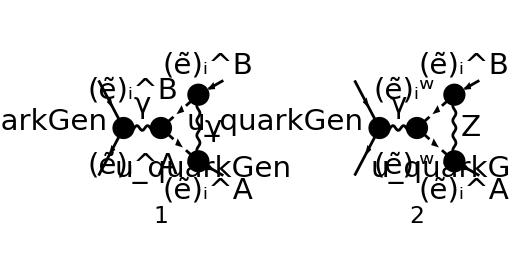

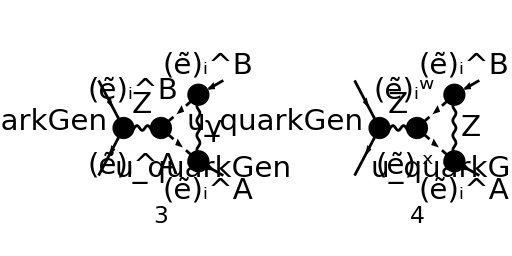

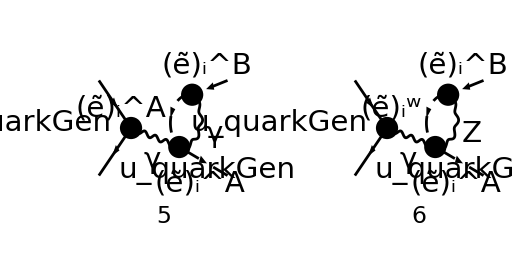

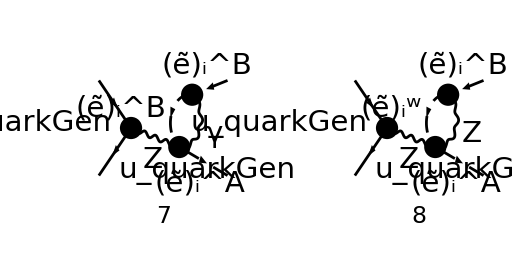

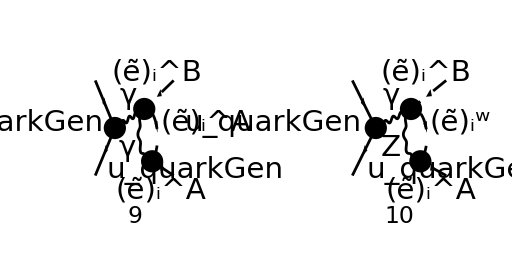

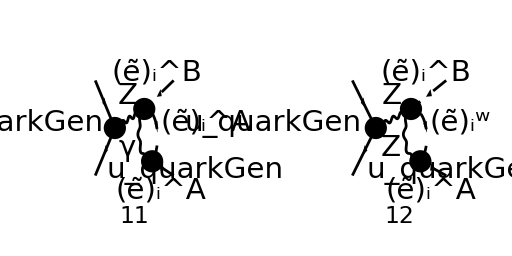

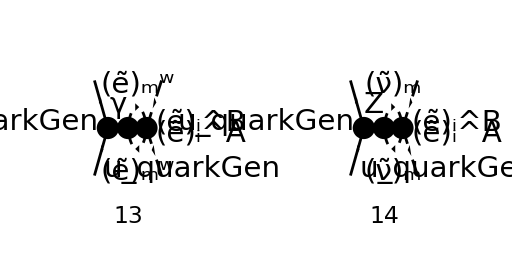

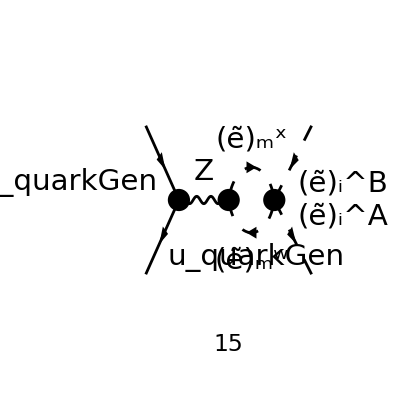

```mathematica
diags[0]=InsertFields[
CreateTopologies[1,2->2,ExcludeTopologies->{WFCorrections,Tadpoles, SelfEnergies}],
{F[3,{quarkGen}],-F[3,{quarkGen}]}->{-S[12,{B,i}],S[12,{A,i}]},
Model->MSSM,
InsertionLevel->{Classes},
ExcludeParticles->{S[1|2|3|4|5|6|13|14],F[3|4|11|12],V[3],U[1|2|3|4]}
(*
	S[1,...,6]=Higgs bosons,
	S[13,14]=squarks,
	F[3,4]=quarks (since we only want slepton-side corrections for now),
	F[11,12]=gauginos,
	V[3]=W boson,
	U[1,...,4]=ghosts,
*)
];
Paint[
diags[0],
ColumnsXRows->{2,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,256}
];
```

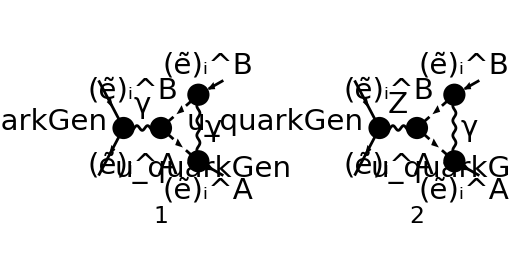

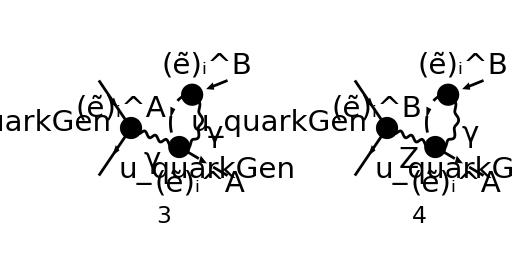

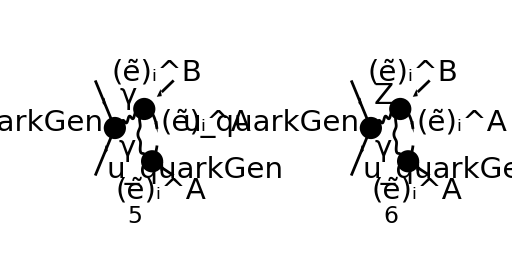

```mathematica
diags[1]=DiagramExtract[diags[0],{1,3,5,7,9,11}];
Paint[
diags[1],
ColumnsXRows->{2,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,256}
];
```

```mathematica
Mlist[0]=FCFAConvert[
CreateFeynAmp[diags[1]],
IncomingMomenta->{p1,p2},
OutgoingMomenta->{k1,k2},
LoopMomenta->{kloop},
ChangeDimension->D,
UndoChiralSplittings->True,
List->True,
Contract->True,
DropSumOver->True,
SMP->True
]/.{MQU[quarkGen]->0}
```

{-((ⅈ (φ(-p_2)).(γ·(-k_1+k_2-2 kloop)).(φ(p_1)) IndexDelta(A,B) (4 (k_1·k_2)-2 (k_1·kloop)+2 (k_2·kloop)-kloop^2) e^4 δ_Col1Col2)/(24 π^4 kloop^2.((k_1+kloop)^2-m_l_iB^2).((kloop-k_2)^2-m_l_iA^2) (k_1+k_2)^2)),-(((φ(-p_2)).((2 ⅈ (γ·(-k_1+k_2-2 kloop)).(γ̄)^6 e (sin(θ_W)) δ_Col1Col2)/(3 (cos(θ_W)))+(ⅈ (γ·(-k_1+k_2-2 kloop)).(γ̄)^7 e (4 (sin(θ_W))^2-3) δ_Col1Col2)/(6 (cos(θ_W)) (sin(θ_W)))).(φ(p_1)) (4 (k_1·k_2)-2 (k_1·kloop)+2 (k_2·kloop)-kloop^2) e^3 (2 Conjugate[(USf(2,i)(B,2))] USf(2,i)(A,2) (sin(θ_W))^2+Conjugate[(USf(2,i)(B,1))] (2 (sin(θ_W))^2-1) USf(2,i)(A,1)))/(32 π^4 kloop^2.((k_1+kloop)^2-m_l_iB^2).((kloop-k_2)^2-m_l_iA^2) ((k_1+k_2)^2-m_Z^2) (cos(θ_W)) (sin(θ_W)))),-(ⅈ (φ(-p_2)).(γ·(kloop-k_1)).(φ(p_1)) IndexDelta(A,B) e^4 δ_Col1Col2)/(12 π^4 (kloop^2-m_l_iA^2).(k_1+kloop)^2 (k_1+k_2)^2),-(((φ(-p_2)).((2 ⅈ (γ·(kloop-k_1)).(γ̄)^6 e (sin(θ_W)) δ_Col1Col2)/(3 (cos(θ_W)))+(ⅈ (γ·(kloop-k_1)).(γ̄)^7 e (4 (sin(θ_W))^2-3) δ_Col1Col2)/(6 (cos(θ_W)) (sin(θ_W)))).(φ(p_1)) e^3 (2 Conjugate[(USf(2,i)(B,2))] USf(2,i)(A,2) (sin(θ_W))^2+Conjugate[(USf(2,i)(B,1))] (2 (sin(θ_W))^2-1) USf(2,i)(A,1)))/(16 π^4 (kloop^2-m_l_iB^2).(k_1+kloop)^2 ((k_1+k_2)^2-m_Z^2) (cos(θ_W)) (sin(θ_W)))),(ⅈ (φ(-p_2)).(γ·(kloop-k_2)).(φ(p_1)) IndexDelta(A,B) e^4 δ_Col1Col2)/(12 π^4 (kloop^2-m_l_iA^2).(k_2+kloop)^2 (k_1+k_2)^2),((φ(-p_2)).((2 ⅈ (γ·(kloop-k_2)).(γ̄)^6 e (sin(θ_W)) δ_Col1Col2)/(3 (cos(θ_W)))+(ⅈ (γ·(kloop-k_2)).(γ̄)^7 e (4 (sin(θ_W))^2-3) δ_Col1Col2)/(6 (cos(θ_W)) (sin(θ_W)))).(φ(p_1)) e^3 (2 Conjugate[(USf(2,i)(B,2))] USf(2,i)(A,2) (sin(θ_W))^2+Conjugate[(USf(2,i)(B,1))] (2 (sin(θ_W))^2-1) USf(2,i)(A,1)))/(16 π^4 (kloop^2-m_l_iA^2).(k_2+kloop)^2 ((k_1+k_2)^2-m_Z^2) (cos(θ_W)) (sin(θ_W)))}

## 4-point diagrams

### Only photon parts

```mathematica
FCClearScalarProducts[];
```

```mathematica
M23γlist[0]=Mlist[0][[{3,5}]] 3/2 SMP["e_Q"]
```

{-(ⅈ e^4 e_Q δ_Col1Col2 IndexDelta(A,B) (φ(-p_2)).(γ·(kloop-k_1)).(φ(p_1)))/(8 π^4 (k_1+k_2)^2 (kloop^2-m_l_iA^2).(k_1+kloop)^2),(ⅈ e^4 e_Q δ_Col1Col2 IndexDelta(A,B) (φ(-p_2)).(γ·(kloop-k_2)).(φ(p_1)))/(8 π^4 (k_1+k_2)^2 (kloop^2-m_l_iA^2).(k_2+kloop)^2)}

```mathematica
M2γ[0]=M23γlist[0][[1]]
M3γ[0]=M23γlist[0][[2]]
```

-(ⅈ e^4 e_Q δ_Col1Col2 IndexDelta(A,B) (φ(-p_2)).(γ·(kloop-k_1)).(φ(p_1)))/(8 π^4 (k_1+k_2)^2 (kloop^2-m_l_iA^2).(k_1+kloop)^2)

(ⅈ e^4 e_Q δ_Col1Col2 IndexDelta(A,B) (φ(-p_2)).(γ·(kloop-k_2)).(φ(p_1)))/(8 π^4 (k_1+k_2)^2 (kloop^2-m_l_iA^2).(k_2+kloop)^2)

```mathematica
M2γ[1]=M2γ[0]//FeynAmpDenominatorSplit//ReplaceAll[#,{FeynAmpDenominator[PropagatorDenominator[Momentum[kloop,D],MSf[A,2,i]]]->FeynAmpDenominator[PropagatorDenominator[Momentum[kloop,D],MSf[B,2,i]]]}]&
```

-(ⅈ e^4 e_Q δ_Col1Col2 IndexDelta(A,B) (φ(-p_2)).(γ·(kloop-k_1)).(φ(p_1)))/(8 π^4 (k_1+k_2)^2 (k_1+kloop)^2 (kloop^2-m_l_iB^2))

```mathematica
M23γ[0]=M2γ[1]+M3γ[0]//FeynAmpDenominatorSplit
```

(ⅈ e^4 e_Q δ_Col1Col2 IndexDelta(A,B) (φ(-p_2)).(γ·(kloop-k_2)).(φ(p_1)))/(8 π^4 (k_1+k_2)^2 (k_2+kloop)^2 (kloop^2-m_l_iA^2))-(ⅈ e^4 e_Q δ_Col1Col2 IndexDelta(A,B) (φ(-p_2)).(γ·(kloop-k_1)).(φ(p_1)))/(8 π^4 (k_1+k_2)^2 (k_1+kloop)^2 (kloop^2-m_l_iB^2))

```mathematica
M23γ[1]=M23γ[0]//TID[#,kloop,ToPaVe->True]&
```

-(e^4 e_Q δ_Col1Col2 IndexDelta(A,B) A_0(m_l_iA^2) (φ(-p_2)).(γ·k_2).(φ(p_1)))/(16 π^2 k_2^2 (k_1+k_2)^2)+(e^4 e_Q δ_Col1Col2 IndexDelta(A,B) A_0(m_l_iB^2) (φ(-p_2)).(γ·k_1).(φ(p_1)))/(16 π^2 k_1^2 (k_1+k_2)^2)+(e^4 e_Q δ_Col1Col2 IndexDelta(A,B) (m_l_iA^2+3 k_2^2) B_0(k_2^2,0,m_l_iA^2) (φ(-p_2)).(γ·k_2).(φ(p_1)))/(16 π^2 k_2^2 (k_1+k_2)^2)+-(e^4 e_Q δ_Col1Col2 IndexDelta(A,B) (m_l_iB^2+3 k_1^2) B_0(k_1^2,0,m_l_iB^2) (φ(-p_2)).(γ·k_1).(φ(p_1)))/(16 π^2 k_1^2 (k_1+k_2)^2)

```mathematica
M23γ[2]=M23γ[1]//PaVeOrder//Simplify
```

1/(16 π^2 k_1^2 k_2^2 (k_1+k_2)^2)e^4 e_Q δ_Col1Col2 IndexDelta(A,B) (k_1^2 (φ(-p_2)).(γ·k_2).(φ(p_1)) ((m_l_iA^2+3 k_2^2) B_0(k_2^2,0,m_l_iA^2)-A_0(m_l_iA^2))+k_2^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) (A_0(m_l_iB^2)-(m_l_iB^2+3 k_1^2) B_0(k_1^2,0,m_l_iB^2)))

Impose momentum conservation and Dirac equation substitute .

```mathematica
M23γ[3]=M23γ[2]//ReplaceAll[#,{DiracGamma[Momentum[k2,D],D]->DiracGamma[Momentum[p1+p2-k1,D],D]}]&//DiracSimplify//Simplify
```

1/(16 π^2 k_1^2 k_2^2 (k_1+k_2)^2)e^4 e_Q δ_Col1Col2 IndexDelta(A,B) (φ(-p_2)).(γ·k_1).(φ(p_1)) (k_1^2 (-3 k_2^2 (B_0(k_2^2,0,m_l_iA^2)+B_0(k_1^2,0,m_l_iB^2))+m_l_iA^2 (-B_0(k_2^2,0,m_l_iA^2))+A_0(m_l_iA^2))+k_2^2 (A_0(m_l_iB^2)-m_l_iB^2 B_0(k_1^2,0,m_l_iB^2)))

### Only Z-boson parts

```mathematica
M23Zlist[0]=Mlist[0][[{4,6}]]//ZSimplify
```

{(e^3 Z_l_i^AB (φ(-p_2)).(2 ⅈ e δ_Col1Col2 (Z_q_L (γ·(kloop-k_1)).(γ̄)^7+Z_q_R (γ·(kloop-k_1)).(γ̄)^6))/((cos(θ_W)) (sin(θ_W))).(φ(p_1)))/(8 π^4 (cos(θ_W)) (sin(θ_W)) ((k_1+k_2)^2-m_Z^2) (kloop^2-m_l_iB^2).(k_1+kloop)^2),-(e^3 Z_l_i^AB (φ(-p_2)).(2 ⅈ e δ_Col1Col2 (Z_q_L (γ·(kloop-k_2)).(γ̄)^7+Z_q_R (γ·(kloop-k_2)).(γ̄)^6))/((cos(θ_W)) (sin(θ_W))).(φ(p_1)))/(8 π^4 (cos(θ_W)) (sin(θ_W)) ((k_1+k_2)^2-m_Z^2) (kloop^2-m_l_iA^2).(k_2+kloop)^2)}

```mathematica
M23Z[0]=Total[M23Zlist[0]]
```

(e^3 Z_l_i^AB (φ(-p_2)).(2 ⅈ e δ_Col1Col2 (Z_q_L (γ·(kloop-k_1)).(γ̄)^7+Z_q_R (γ·(kloop-k_1)).(γ̄)^6))/((cos(θ_W)) (sin(θ_W))).(φ(p_1)))/(8 π^4 (cos(θ_W)) (sin(θ_W)) ((k_1+k_2)^2-m_Z^2) (kloop^2-m_l_iB^2).(k_1+kloop)^2)-(e^3 Z_l_i^AB (φ(-p_2)).(2 ⅈ e δ_Col1Col2 (Z_q_L (γ·(kloop-k_2)).(γ̄)^7+Z_q_R (γ·(kloop-k_2)).(γ̄)^6))/((cos(θ_W)) (sin(θ_W))).(φ(p_1)))/(8 π^4 (cos(θ_W)) (sin(θ_W)) ((k_1+k_2)^2-m_Z^2) (kloop^2-m_l_iA^2).(k_2+kloop)^2)

```mathematica
M23Z[1]=M23Z[0]//TID[#,kloop,ToPaVe->True]&//PaVeOrder//Simplify
```

(e^4 δ_Col1Col2 Z_l_i^AB (k_1^2 Z_q_L (φ(-p_2)).(γ·k_2).(γ̄)^7.(φ(p_1)) (A_0(m_l_iA^2)-(m_l_iA^2+3 k_2^2) B_0(k_2^2,0,m_l_iA^2))+k_1^2 Z_q_R (φ(-p_2)).(γ·k_2).(γ̄)^6.(φ(p_1)) (A_0(m_l_iA^2)-(m_l_iA^2+3 k_2^2) B_0(k_2^2,0,m_l_iA^2))-(k_2^2 (A_0(m_l_iB^2)-(m_l_iB^2+3 k_1^2) B_0(k_1^2,0,m_l_iB^2)) (Z_q_L (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1))+Z_q_R (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1))))))/(8 π^2 k_1^2 k_2^2 (cos(θ_W))^2 (sin(θ_W))^2 ((k_1+k_2)^2-m_Z^2))

Impose momentum conservation and Dirac equation substitute .

```mathematica
M23Z[2]=M23Z[1]//ReplaceAll[#,{DiracGamma[Momentum[k2,D],D]->DiracGamma[Momentum[p1+p2-k1,D],D]}]&//DiracSimplify//Simplify
```

-((e^4 δ_Col1Col2 Z_l_i^AB (k_1^2 (-3 k_2^2 (B_0(k_2^2,0,m_l_iA^2)+B_0(k_1^2,0,m_l_iB^2))+m_l_iA^2 (-B_0(k_2^2,0,m_l_iA^2))+A_0(m_l_iA^2))+k_2^2 (A_0(m_l_iB^2)-m_l_iB^2 B_0(k_1^2,0,m_l_iB^2))) (Z_q_L (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1))+Z_q_R (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1))))/(8 π^2 k_1^2 k_2^2 (cos(θ_W))^2 (sin(θ_W))^2 ((k_1+k_2)^2-m_Z^2)))

### Combining the 4-point diagrams

```mathematica
FCClearScalarProducts[];
SPD[k1]=MSf[B,2,i]^2;
SPD[k2]=MSf[A,2,i]^2;
```

```mathematica
M23[0]=M23γ[3]+M23Z[2]//PropagatorDenominatorExplicit//PaVeOrder//Simplify
```

-((e^4 δ_Col1Col2 (m_l_iB^2 (A_0(m_l_iA^2)-4 m_l_iA^2 (B_0(m_l_iA^2,0,m_l_iA^2)+B_0(m_l_iB^2,0,m_l_iB^2)))+m_l_iA^2 A_0(m_l_iB^2)) (2 Z_q_L Z_l_i^AB (m_l_iA^2+m_l_iB^2+2 (k_1·k_2)) (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1))+2 Z_q_R Z_l_i^AB (m_l_iA^2+m_l_iB^2+2 (k_1·k_2)) (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1))+e_Q (cos(θ_W))^2 (sin(θ_W))^2 IndexDelta(A,B) (-(φ(-p_2)).(γ·k_1).(φ(p_1))) (m_l_iA^2+m_l_iB^2+2 (k_1·k_2)-m_Z^2)))/(16 π^2 (cos(θ_W))^2 m_l_iA^2 m_l_iB^2 (sin(θ_W))^2 (m_l_iA^2+m_l_iB^2+2 (k_1·k_2)) (m_l_iA^2+m_l_iB^2+2 (k_1·k_2)-m_Z^2)))

#### Compare to hand calculation

```mathematica
MLOγ[0]=2SMP["e"]^2SMP["e_Q"]SUNFDelta[SUNFIndex[Col1],SUNFIndex[Col2]]IndexDelta[A,B]FAD[k1+k2]SpinorVBarD[p2].GSD[k1].SpinorUD[p1]//PropagatorDenominatorExplicit//Simplify
```

(2 e^2 e_Q δ_Col1Col2 IndexDelta(A,B) (φ(-p_2)).(γ·k_1).(φ(p_1)))/(m_l_iA^2+m_l_iB^2+2 (k_1·k_2))

```mathematica
MLOZ[0]=-2SMP["e"]^2ZliAB SUNFDelta[SUNFIndex[Col1],SUNFIndex[Col2]]/(SMP["sin_W"]^2SMP["cos_W"]^2)FAD[{k1+k2,SMP["m_Z"]}]2SpinorVBarD[p2].GSD[k1].(Zql GAD[7]+Zqr GAD[6]).SpinorUD[p1]//PropagatorDenominatorExplicit//Simplify
```

-(4 e^2 δ_Col1Col2 Z_l_i^AB (φ(-p_2)).(γ·k_1).((γ̄)^7 Z_q_L+(γ̄)^6 Z_q_R).(φ(p_1)))/((cos(θ_W))^2 (sin(θ_W))^2 (m_l_iA^2+m_l_iB^2+2 (k_1·k_2)-m_Z^2))

```mathematica
MLO[0]=MLOγ[0]+MLOZ[0]
```

(2 e^2 e_Q δ_Col1Col2 IndexDelta(A,B) (φ(-p_2)).(γ·k_1).(φ(p_1)))/(m_l_iA^2+m_l_iB^2+2 (k_1·k_2))-(4 e^2 δ_Col1Col2 Z_l_i^AB (φ(-p_2)).(γ·k_1).((γ̄)^7 Z_q_L+(γ̄)^6 Z_q_R).(φ(p_1)))/((cos(θ_W))^2 (sin(θ_W))^2 (m_l_iA^2+m_l_iB^2+2 (k_1·k_2)-m_Z^2))

```mathematica
PVpart23=A0[MSf[A,2,i]^2]/MSf[A,2,i]^2+A0[MSf[B,2,i]^2]/MSf[B,2,i]^2-4B0[SPD[k2],MSf[A,2,i]^2,0]-4B0[SPD[k1],MSf[B,2,i]^2,0]
```

-4 B_0(m_l_iA^2,0,m_l_iA^2)-4 B_0(m_l_iB^2,0,m_l_iB^2)+(A_0(m_l_iA^2))/m_l_iA^2+(A_0(m_l_iB^2))/m_l_iB^2

```mathematica
M23Hand[0]=MLO[0]SMP["e"]^2/(32 Pi^2)PVpart23//PaVeOrder//Simplify
```

-((e^4 δ_Col1Col2 (m_l_iB^2 (A_0(m_l_iA^2)-4 m_l_iA^2 (B_0(m_l_iA^2,0,m_l_iA^2)+B_0(m_l_iB^2,0,m_l_iB^2)))+m_l_iA^2 A_0(m_l_iB^2)) (2 Z_q_L Z_l_i^AB (m_l_iA^2+m_l_iB^2+2 (k_1·k_2)) (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1))+2 Z_q_R Z_l_i^AB (m_l_iA^2+m_l_iB^2+2 (k_1·k_2)) (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1))+e_Q (cos(θ_W))^2 (sin(θ_W))^2 IndexDelta(A,B) (-(φ(-p_2)).(γ·k_1).(φ(p_1))) (m_l_iA^2+m_l_iB^2+2 (k_1·k_2)-m_Z^2)))/(16 π^2 (cos(θ_W))^2 m_l_iA^2 m_l_iB^2 (sin(θ_W))^2 (m_l_iA^2+m_l_iB^2+2 (k_1·k_2)) (m_l_iA^2+m_l_iB^2+2 (k_1·k_2)-m_Z^2)))

```mathematica
FCCompareResults[{M23[0]},{M23Hand[0]},Text->{"Compare to hand calculations:","Correct!","Wrong!"},
Interrupt->{Hold[Quit[1]],Automatic}];
```

Compare to hand calculations: Correct!

## Triangle diagrams

### Only photon part

```mathematica
FCClearScalarProducts[];
```

```mathematica
M1γ[0]=Mlist[0][[1]] 3/2 SMP["e_Q"]
```

-((ⅈ e^4 e_Q δ_Col1Col2 (-2 (k_1·kloop)+2 (k_2·kloop)+4 (k_1·k_2)-kloop^2) IndexDelta(A,B) (φ(-p_2)).(γ·(-k_1+k_2-2 kloop)).(φ(p_1)))/(16 π^4 (k_1+k_2)^2 kloop^2.((k_1+kloop)^2-m_l_iB^2).((kloop-k_2)^2-m_l_iA^2)))

Use momentum conservation and Dirac equation to simplify

```mathematica
M1γ[1]=M1γ[0]//ReplaceAll[#,{DiracGamma[Momentum[-k1+k2-2kloop,D],D]->DiracGamma[Momentum[-k1+p1+p2-k1-2kloop,D],D]}]&//DiracSimplify//Simplify
```

(ⅈ e^4 e_Q δ_Col1Col2 (-2 (k_1·kloop)+2 (k_2·kloop)+4 (k_1·k_2)-kloop^2) IndexDelta(A,B) ((φ(-p_2)).(γ·k_1).(φ(p_1))+(φ(-p_2)).(γ·kloop).(φ(p_1))))/(8 π^4 (k_1+k_2)^2 kloop^2.((k_1+kloop)^2-m_l_iB^2).((k_2-kloop)^2-m_l_iA^2))

```mathematica
M1γ[2]=M1γ[1]//TID[#,kloop,ToPaVe->True]&//PaVeOrder//Simplify
```

1/(16 π^2 (k_1+k_2)^2)IndexDelta(A,B) ((((φ(-p_2)).(γ·k_2).(φ(p_1)))/k_2^2-((φ(-p_2)).(γ·(k_1+k_2)).(φ(p_1)))/(k_1^2+2 (k_1·k_2)+k_2^2)) A_0(m_l_iA^2)+(((φ(-p_2)).(γ·(k_1+k_2)).(φ(p_1)))/(k_1^2+2 (k_1·k_2)+k_2^2)-((φ(-p_2)).(γ·k_1).(φ(p_1)))/k_1^2) A_0(m_l_iB^2)+1/(k_1^2 (k_1^2 k_2^2-(k_1·k_2)^2))((φ(-p_2)).(γ·k_2).(φ(p_1)) (-m_l_iA^2-m_l_iB^2+k_1^2+4 (k_1·k_2)+k_2^2) k_1^4+(φ(-p_2)).(γ·k_1).(φ(p_1)) (k_1^2 (k_1·k_2) m_l_iA^2+m_l_iB^2 (k_1^2 (k_1·k_2+k_2^2)-(k_1·k_2)^2)-k_1^2 (k_1^2 (k_1·k_2-k_2^2)+(k_1·k_2) (5 (k_1·k_2)+k_2^2)))) B_0(k_1^2,0,m_l_iB^2)+1/(k_2^2 (k_1^2 k_2^2-(k_1·k_2)^2))((φ(-p_2)).(γ·k_1).(φ(p_1)) k_2^2 (-2 (k_1·k_2)^2-4 k_2^2 (k_1·k_2)+(m_l_iA^2+m_l_iB^2+k_1^2-k_2^2) k_2^2)+(φ(-p_2)).(γ·k_2).(φ(p_1)) (((k_1·k_2)^2-k_2^2 (k_1·k_2)-k_1^2 k_2^2) m_l_iA^2+k_2^2 (-(k_1·k_2) m_l_iB^2+k_1^2 (k_1·k_2+k_2^2)+(k_1·k_2) (3 (k_1·k_2)+k_2^2)))) B_0(k_2^2,0,m_l_iA^2)+((2 (φ(-p_2)).(γ·(k_1+k_2)).(φ(p_1)) (k_1·k_2)^3-(φ(-p_2)).(γ·(k_1+k_2)).(φ(p_1)) m_l_iA^2 (k_1·k_2)^2+(φ(-p_2)).(γ·(k_1+k_2)).(φ(p_1)) m_l_iB^2 (k_1·k_2)^2+(φ(-p_2)).(γ·(k_1+k_2)).(φ(p_1)) k_1^2 (k_1·k_2)^2+8 (φ(-p_2)).(γ·k_1).(φ(p_1)) k_2^2 (k_1·k_2)^2+(φ(-p_2)).(γ·(k_1+k_2)).(φ(p_1)) k_2^2 (k_1·k_2)^2+6 (φ(-p_2)).(γ·k_1).(φ(p_1)) k_2^4 (k_1·k_2)-2 (φ(-p_2)).(γ·k_1).(φ(p_1)) m_l_iA^2 k_2^2 (k_1·k_2)-2 (φ(-p_2)).(γ·k_1).(φ(p_1)) m_l_iB^2 k_2^2 (k_1·k_2)+6 (φ(-p_2)).(γ·k_1).(φ(p_1)) k_1^2 k_2^2 (k_1·k_2)-2 (φ(-p_2)).(γ·(k_1+k_2)).(φ(p_1)) k_1^2 k_2^2 (k_1·k_2)+(φ(-p_2)).(γ·(k_1-k_2)).(φ(p_1)) (k_1^2+2 (k_1·k_2)+k_2^2) (-m_l_iA^2-m_l_iB^2+k_1^2+4 (k_1·k_2)+k_2^2) (k_1·k_2)+(φ(-p_2)).(γ·k_1).(φ(p_1)) k_2^6-(φ(-p_2)).(γ·k_1).(φ(p_1)) m_l_iA^2 k_2^4-(φ(-p_2)).(γ·k_1).(φ(p_1)) m_l_iB^2 k_2^4+2 (φ(-p_2)).(γ·k_1).(φ(p_1)) k_1^2 k_2^4-(φ(-p_2)).(γ·(k_1+k_2)).(φ(p_1)) k_1^2 k_2^4+(φ(-p_2)).(γ·k_1).(φ(p_1)) k_1^4 k_2^2-(φ(-p_2)).(γ·(k_1+k_2)).(φ(p_1)) k_1^4 k_2^2-(φ(-p_2)).(γ·k_1).(φ(p_1)) m_l_iA^2 k_1^2 k_2^2+(φ(-p_2)).(γ·(k_1+k_2)).(φ(p_1)) m_l_iA^2 k_1^2 k_2^2-(φ(-p_2)).(γ·k_1).(φ(p_1)) m_l_iB^2 k_1^2 k_2^2-(φ(-p_2)).(γ·(k_1+k_2)).(φ(p_1)) m_l_iB^2 k_1^2 k_2^2+(φ(-p_2)).(γ·k_2).(φ(p_1)) k_1^2 (m_l_iA^2+m_l_iB^2-k_1^2-4 (k_1·k_2)-k_2^2) (k_1^2+2 (k_1·k_2)+k_2^2)) B_0(k_1^2+2 (k_1·k_2)+k_2^2,m_l_iA^2,m_l_iB^2))/((k_1^2+2 (k_1·k_2)+k_2^2) (k_1^2 k_2^2-(k_1·k_2)^2))-1/(k_1^2 k_2^2-(k_1·k_2)^2)(m_l_iA^2+m_l_iB^2-k_1^2-4 (k_1·k_2)-k_2^2) ((φ(-p_2)).(γ·k_2).(φ(p_1)) (k_1^2 m_l_iA^2+m_l_iB^2 (k_1·k_2)-k_1^2 (k_1·k_2+k_2^2))-(φ(-p_2)).(γ·k_1).(φ(p_1)) ((k_1·k_2) m_l_iA^2-2 (k_1·k_2)^2+(m_l_iB^2+k_1^2) k_2^2-(k_1·k_2) k_2^2)) C_0(k_1^2,k_2^2,k_1^2+2 (k_1·k_2)+k_2^2,m_l_iB^2,0,m_l_iA^2)) e^4 e_Q δ_Col1Col2

Simplify by using momentum conservation and Dirac equation again to get rid of all γ.k2’s

```mathematica
M1γ[3]=M1γ[2]//DiracGammaExpand//ReplaceAll[#,{DiracGamma[Momentum[k2,D],D]->DiracGamma[Momentum[p1+p2-k1,D],D]}]&//DiracSimplify//Simplify
```

((φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) (k_2^2 (-B_0(k_1^2,0,m_l_iB^2)+B_0(k_1^2+2 (k_1·k_2)+k_2^2,m_l_iA^2,m_l_iB^2)+(k_1·k_2-m_l_iA^2) C_0(k_1^2,k_2^2,k_1^2+2 (k_1·k_2)+k_2^2,m_l_iB^2,0,m_l_iA^2)) k_1^6-k_2^2 (-C_0(k_1^2,k_2^2,k_1^2+2 (k_1·k_2)+k_2^2,m_l_iB^2,0,m_l_iA^2) m_l_iA^4-(C_0(k_1^2,k_2^2,k_1^2+2 (k_1·k_2)+k_2^2,m_l_iB^2,0,m_l_iA^2) m_l_iB^2+B_0(k_1^2,0,m_l_iB^2)+B_0(k_2^2,0,m_l_iA^2)-B_0(k_1^2+2 (k_1·k_2)+k_2^2,m_l_iA^2,m_l_iB^2)-6 (k_1·k_2) C_0(k_1^2,k_2^2,k_1^2+2 (k_1·k_2)+k_2^2,m_l_iB^2,0,m_l_iA^2)-k_2^2 C_0(k_1^2,k_2^2,k_1^2+2 (k_1·k_2)+k_2^2,m_l_iB^2,0,m_l_iA^2)) m_l_iA^2+A_0(m_l_iA^2)-m_l_iB^2 B_0(k_1^2,0,m_l_iB^2)+5 (k_1·k_2) B_0(k_1^2,0,m_l_iB^2)+(k_1·k_2) B_0(k_2^2,0,m_l_iA^2)+m_l_iB^2 B_0(k_1^2+2 (k_1·k_2)+k_2^2,m_l_iA^2,m_l_iB^2)-6 (k_1·k_2) B_0(k_1^2+2 (k_1·k_2)+k_2^2,m_l_iA^2,m_l_iB^2)-2 k_2^2 B_0(k_1^2+2 (k_1·k_2)+k_2^2,m_l_iA^2,m_l_iB^2)-6 (k_1·k_2)^2 C_0(k_1^2,k_2^2,k_1^2+2 (k_1·k_2)+k_2^2,m_l_iB^2,0,m_l_iA^2)+2 m_l_iB^2 (k_1·k_2) C_0(k_1^2,k_2^2,k_1^2+2 (k_1·k_2)+k_2^2,m_l_iB^2,0,m_l_iA^2)+m_l_iB^2 k_2^2 C_0(k_1^2,k_2^2,k_1^2+2 (k_1·k_2)+k_2^2,m_l_iB^2,0,m_l_iA^2)-2 (k_1·k_2) k_2^2 C_0(k_1^2,k_2^2,k_1^2+2 (k_1·k_2)+k_2^2,m_l_iB^2,0,m_l_iA^2)) k_1^4+(8 k_2^2 C_0(k_1^2,k_2^2,k_1^2+2 (k_1·k_2)+k_2^2,m_l_iB^2,0,m_l_iA^2) (k_1·k_2)^3+(-B_0(k_2^2,0,m_l_iA^2) m_l_iA^2+A_0(m_l_iA^2)+6 k_2^4 C_0(k_1^2,k_2^2,k_1^2+2 (k_1·k_2)+k_2^2,m_l_iB^2,0,m_l_iA^2)-k_2^2 (6 C_0(k_1^2,k_2^2,k_1^2+2 (k_1·k_2)+k_2^2,m_l_iB^2,0,m_l_iA^2) m_l_iA^2+5 B_0(k_1^2,0,m_l_iB^2)+5 B_0(k_2^2,0,m_l_iA^2)-8 B_0(k_1^2+2 (k_1·k_2)+k_2^2,m_l_iA^2,m_l_iB^2)+6 m_l_iB^2 C_0(k_1^2,k_2^2,k_1^2+2 (k_1·k_2)+k_2^2,m_l_iB^2,0,m_l_iA^2))) (k_1·k_2)^2+k_2^2 (C_0(k_1^2,k_2^2,k_1^2+2 (k_1·k_2)+k_2^2,m_l_iB^2,0,m_l_iA^2) m_l_iA^4+(2 C_0(k_1^2,k_2^2,k_1^2+2 (k_1·k_2)+k_2^2,m_l_iB^2,0,m_l_iA^2) m_l_iB^2+B_0(k_1^2,0,m_l_iB^2)+B_0(k_2^2,0,m_l_iA^2)-2 B_0(k_1^2+2 (k_1·k_2)+k_2^2,m_l_iA^2,m_l_iB^2)-2 k_2^2 C_0(k_1^2,k_2^2,k_1^2+2 (k_1·k_2)+k_2^2,m_l_iB^2,0,m_l_iA^2)) m_l_iA^2+m_l_iB^4 C_0(k_1^2,k_2^2,k_1^2+2 (k_1·k_2)+k_2^2,m_l_iB^2,0,m_l_iA^2)+m_l_iB^2 (B_0(k_1^2,0,m_l_iB^2)+B_0(k_2^2,0,m_l_iA^2)-2 B_0(k_1^2+2 (k_1·k_2)+k_2^2,m_l_iA^2,m_l_iB^2)-6 k_2^2 C_0(k_1^2,k_2^2,k_1^2+2 (k_1·k_2)+k_2^2,m_l_iB^2,0,m_l_iA^2))+k_2^2 (-B_0(k_1^2,0,m_l_iB^2)-5 B_0(k_2^2,0,m_l_iA^2)+6 B_0(k_1^2+2 (k_1·k_2)+k_2^2,m_l_iA^2,m_l_iB^2)+k_2^2 C_0(k_1^2,k_2^2,k_1^2+2 (k_1·k_2)+k_2^2,m_l_iB^2,0,m_l_iA^2))) (k_1·k_2)+k_2^4 (C_0(k_1^2,k_2^2,k_1^2+2 (k_1·k_2)+k_2^2,m_l_iB^2,0,m_l_iA^2) m_l_iB^4+(C_0(k_1^2,k_2^2,k_1^2+2 (k_1·k_2)+k_2^2,m_l_iB^2,0,m_l_iA^2) m_l_iA^2+B_0(k_1^2,0,m_l_iB^2)+B_0(k_2^2,0,m_l_iA^2)-B_0(k_1^2+2 (k_1·k_2)+k_2^2,m_l_iA^2,m_l_iB^2)-k_2^2 C_0(k_1^2,k_2^2,k_1^2+2 (k_1·k_2)+k_2^2,m_l_iB^2,0,m_l_iA^2)) m_l_iB^2-A_0(m_l_iB^2)+(m_l_iA^2-k_2^2) (B_0(k_2^2,0,m_l_iA^2)-B_0(k_1^2+2 (k_1·k_2)+k_2^2,m_l_iA^2,m_l_iB^2)))) k_1^2+(k_1·k_2)^2 k_2^2 (A_0(m_l_iB^2)-m_l_iB^2 B_0(k_1^2,0,m_l_iB^2))) e^4 e_Q δ_Col1Col2)/(16 π^2 k_1^2 k_2^2 (k_1^2 k_2^2-(k_1·k_2)^2) (k_1+k_2)^2)

```mathematica
FCClearScalarProducts[];
SPD[k1]=MSf[B,2,i]^2;
SPD[k2]=MSf[A,2,i]^2;
```

```mathematica
M1γ[4]=M1γ[3]//PropagatorDenominatorExplicit//Simplify
```

-((e^4 e_Q δ_Col1Col2 IndexDelta(A,B) (φ(-p_2)).(γ·k_1).(φ(p_1)) (m_l_iA^2 (2 m_l_iB^2 (k_1·k_2)^2 (-4 (B_0(m_l_iA^2+m_l_iB^2+2 (k_1·k_2),m_l_iA^2,m_l_iB^2)+(k_1·k_2) C_0(m_l_iA^2,m_l_iB^2,m_l_iA^2+m_l_iB^2+2 (k_1·k_2),m_l_iA^2,0,m_l_iB^2))+3 B_0(m_l_iA^2,0,m_l_iA^2)+3 B_0(m_l_iB^2,0,m_l_iB^2))+m_l_iB^4 (4 (k_1·k_2) (B_0(m_l_iB^2,0,m_l_iB^2)-B_0(m_l_iA^2+m_l_iB^2+2 (k_1·k_2),m_l_iA^2,m_l_iB^2))+A_0(m_l_iA^2))-(k_1·k_2)^2 A_0(m_l_iB^2))+m_l_iA^4 m_l_iB^2 (-2 m_l_iB^2 (B_0(m_l_iA^2,0,m_l_iA^2)+B_0(m_l_iB^2,0,m_l_iB^2)-4 (k_1·k_2) C_0(m_l_iA^2,m_l_iB^2,m_l_iA^2+m_l_iB^2+2 (k_1·k_2),m_l_iA^2,0,m_l_iB^2))+4 (k_1·k_2) (B_0(m_l_iA^2,0,m_l_iA^2)-B_0(m_l_iA^2+m_l_iB^2+2 (k_1·k_2),m_l_iA^2,m_l_iB^2))+A_0(m_l_iB^2))-m_l_iB^2 (k_1·k_2)^2 A_0(m_l_iA^2)))/(16 π^2 m_l_iA^2 m_l_iB^2 (m_l_iA^2+m_l_iB^2+2 (k_1·k_2)) (m_l_iA^2 m_l_iB^2-(k_1·k_2)^2)))

### Only Z-boson part

```mathematica
FCClearScalarProducts[];
```

```mathematica
M1Z[0]=Mlist[0][[2]]//ZSimplify
```

(e^3 (-2 (k_1·kloop)+2 (k_2·kloop)+4 (k_1·k_2)-kloop^2) Z_l_i^AB (φ(-p_2)).(2 ⅈ e δ_Col1Col2 (Z_q_L (γ·(-k_1+k_2-2 kloop)).(γ̄)^7+Z_q_R (γ·(-k_1+k_2-2 kloop)).(γ̄)^6))/((cos(θ_W)) (sin(θ_W))).(φ(p_1)))/(16 π^4 (cos(θ_W)) (sin(θ_W)) ((k_1+k_2)^2-m_Z^2) kloop^2.((k_1+kloop)^2-m_l_iB^2).((kloop-k_2)^2-m_l_iA^2))

Use momentum conservation and Dirac equation to simplify

```mathematica
M1Z[1]=M1Z[0]//ReplaceAll[#,{DiracGamma[Momentum[-k1+k2-2kloop,D],D]->DiracGamma[Momentum[-k1+p1+p2-k1-2kloop,D],D]}]&//DiracSimplify//Simplify
```

-((ⅈ e^4 δ_Col1Col2 (-2 (k_1·kloop)+2 (k_2·kloop)+4 (k_1·k_2)-kloop^2) Z_l_i^AB (Z_q_L (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1))+Z_q_R (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1))+Z_q_L (φ(-p_2)).(γ·kloop).(γ̄)^7.(φ(p_1))+Z_q_R (φ(-p_2)).(γ·kloop).(γ̄)^6.(φ(p_1))))/(4 π^4 (cos(θ_W))^2 (sin(θ_W))^2 ((k_1+k_2)^2-m_Z^2) kloop^2.((k_1+kloop)^2-m_l_iB^2).((k_2-kloop)^2-m_l_iA^2)))

```mathematica
M1Z[2]=M1Z[1]//TID[#,kloop,ToPaVe->True]&//PaVeOrder//Simplify
```

(Z_l_i^AB ((-(Z_q_R (φ(-p_2)).(γ·k_2).(γ̄)^6.(φ(p_1)))/k_2^2-(Z_q_L (φ(-p_2)).(γ·k_2).(γ̄)^7.(φ(p_1)))/k_2^2+(Z_q_R (φ(-p_2)).(γ·(k_1+k_2)).(γ̄)^6.(φ(p_1))+Z_q_L (φ(-p_2)).(γ·(k_1+k_2)).(γ̄)^7.(φ(p_1)))/(k_1^2+2 (k_1·k_2)+k_2^2)) A_0(m_l_iA^2)+((Z_q_R (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)))/k_1^2+(Z_q_L (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1)))/k_1^2-(Z_q_R (φ(-p_2)).(γ·(k_1+k_2)).(γ̄)^6.(φ(p_1))+Z_q_L (φ(-p_2)).(γ·(k_1+k_2)).(γ̄)^7.(φ(p_1)))/(k_1^2+2 (k_1·k_2)+k_2^2)) A_0(m_l_iB^2)-1/(k_1^2 (k_1^2 k_2^2-(k_1·k_2)^2))(Z_q_R (φ(-p_2)).(γ·k_2).(γ̄)^6.(φ(p_1)) (-m_l_iA^2-m_l_iB^2+k_1^2+4 (k_1·k_2)+k_2^2) k_1^4+Z_q_L (φ(-p_2)).(γ·k_2).(γ̄)^7.(φ(p_1)) (-m_l_iA^2-m_l_iB^2+k_1^2+4 (k_1·k_2)+k_2^2) k_1^4+(Z_q_R (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1))+Z_q_L (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1))) (k_1^2 (k_1·k_2) m_l_iA^2+m_l_iB^2 (k_1^2 (k_1·k_2+k_2^2)-(k_1·k_2)^2)-k_1^2 (k_1^2 (k_1·k_2-k_2^2)+(k_1·k_2) (5 (k_1·k_2)+k_2^2)))) B_0(k_1^2,0,m_l_iB^2)-1/(k_2^2 (k_1^2 k_2^2-(k_1·k_2)^2))(-((Z_q_R (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1))+Z_q_L (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1))) k_2^2 (2 (k_1·k_2)^2+4 k_2^2 (k_1·k_2)+k_2^2 (-m_l_iA^2-m_l_iB^2-k_1^2+k_2^2)))+Z_q_R (φ(-p_2)).(γ·k_2).(γ̄)^6.(φ(p_1)) (((k_1·k_2)^2-k_2^2 (k_1·k_2)-k_1^2 k_2^2) m_l_iA^2+k_2^2 (-(k_1·k_2) m_l_iB^2+k_1^2 (k_1·k_2+k_2^2)+(k_1·k_2) (3 (k_1·k_2)+k_2^2)))+Z_q_L (φ(-p_2)).(γ·k_2).(γ̄)^7.(φ(p_1)) (((k_1·k_2)^2-k_2^2 (k_1·k_2)-k_1^2 k_2^2) m_l_iA^2+k_2^2 (-(k_1·k_2) m_l_iB^2+k_1^2 (k_1·k_2+k_2^2)+(k_1·k_2) (3 (k_1·k_2)+k_2^2)))) B_0(k_2^2,0,m_l_iA^2)+((-8 Z_q_R (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)) (k_1·k_2)^3-8 Z_q_L (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1)) (k_1·k_2)^3-2 Z_q_R (φ(-p_2)).(γ·(k_1+k_2)).(γ̄)^6.(φ(p_1)) (k_1·k_2)^3-2 Z_q_L (φ(-p_2)).(γ·(k_1+k_2)).(γ̄)^7.(φ(p_1)) (k_1·k_2)^3+2 Z_q_R (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)) m_l_iA^2 (k_1·k_2)^2+2 Z_q_L (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1)) m_l_iA^2 (k_1·k_2)^2+Z_q_R (φ(-p_2)).(γ·(k_1+k_2)).(γ̄)^6.(φ(p_1)) m_l_iA^2 (k_1·k_2)^2+Z_q_L (φ(-p_2)).(γ·(k_1+k_2)).(γ̄)^7.(φ(p_1)) m_l_iA^2 (k_1·k_2)^2+2 Z_q_R (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)) m_l_iB^2 (k_1·k_2)^2+2 Z_q_L (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1)) m_l_iB^2 (k_1·k_2)^2-Z_q_R (φ(-p_2)).(γ·(k_1+k_2)).(γ̄)^6.(φ(p_1)) m_l_iB^2 (k_1·k_2)^2-Z_q_L (φ(-p_2)).(γ·(k_1+k_2)).(γ̄)^7.(φ(p_1)) m_l_iB^2 (k_1·k_2)^2-6 Z_q_R (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)) k_1^2 (k_1·k_2)^2-6 Z_q_L (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1)) k_1^2 (k_1·k_2)^2-Z_q_R (φ(-p_2)).(γ·(k_1+k_2)).(γ̄)^6.(φ(p_1)) k_1^2 (k_1·k_2)^2-Z_q_L (φ(-p_2)).(γ·(k_1+k_2)).(γ̄)^7.(φ(p_1)) k_1^2 (k_1·k_2)^2-14 Z_q_R (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)) k_2^2 (k_1·k_2)^2-14 Z_q_L (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1)) k_2^2 (k_1·k_2)^2-Z_q_R (φ(-p_2)).(γ·(k_1+k_2)).(γ̄)^6.(φ(p_1)) k_2^2 (k_1·k_2)^2-Z_q_L (φ(-p_2)).(γ·(k_1+k_2)).(γ̄)^7.(φ(p_1)) k_2^2 (k_1·k_2)^2-Z_q_R (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)) k_1^4 (k_1·k_2)-Z_q_L (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1)) k_1^4 (k_1·k_2)-7 Z_q_R (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)) k_2^4 (k_1·k_2)-7 Z_q_L (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1)) k_2^4 (k_1·k_2)+Z_q_R (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)) m_l_iA^2 k_1^2 (k_1·k_2)+Z_q_L (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1)) m_l_iA^2 k_1^2 (k_1·k_2)+Z_q_R (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)) m_l_iB^2 k_1^2 (k_1·k_2)+Z_q_L (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1)) m_l_iB^2 k_1^2 (k_1·k_2)+3 Z_q_R (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)) m_l_iA^2 k_2^2 (k_1·k_2)+3 Z_q_L (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1)) m_l_iA^2 k_2^2 (k_1·k_2)+3 Z_q_R (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)) m_l_iB^2 k_2^2 (k_1·k_2)+3 Z_q_L (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1)) m_l_iB^2 k_2^2 (k_1·k_2)-8 Z_q_R (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)) k_1^2 k_2^2 (k_1·k_2)-8 Z_q_L (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1)) k_1^2 k_2^2 (k_1·k_2)+2 Z_q_R (φ(-p_2)).(γ·(k_1+k_2)).(γ̄)^6.(φ(p_1)) k_1^2 k_2^2 (k_1·k_2)+2 Z_q_L (φ(-p_2)).(γ·(k_1+k_2)).(γ̄)^7.(φ(p_1)) k_1^2 k_2^2 (k_1·k_2)-Z_q_R (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)) k_2^6-Z_q_L (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1)) k_2^6+Z_q_R (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)) m_l_iA^2 k_2^4+Z_q_L (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1)) m_l_iA^2 k_2^4+Z_q_R (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)) m_l_iB^2 k_2^4+Z_q_L (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1)) m_l_iB^2 k_2^4-2 Z_q_R (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)) k_1^2 k_2^4-2 Z_q_L (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1)) k_1^2 k_2^4+Z_q_R (φ(-p_2)).(γ·(k_1+k_2)).(γ̄)^6.(φ(p_1)) k_1^2 k_2^4+Z_q_L (φ(-p_2)).(γ·(k_1+k_2)).(γ̄)^7.(φ(p_1)) k_1^2 k_2^4-Z_q_R (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)) k_1^4 k_2^2-Z_q_L (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1)) k_1^4 k_2^2+Z_q_R (φ(-p_2)).(γ·(k_1+k_2)).(γ̄)^6.(φ(p_1)) k_1^4 k_2^2+Z_q_L (φ(-p_2)).(γ·(k_1+k_2)).(γ̄)^7.(φ(p_1)) k_1^4 k_2^2+Z_q_R (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)) m_l_iA^2 k_1^2 k_2^2+Z_q_L (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1)) m_l_iA^2 k_1^2 k_2^2-Z_q_R (φ(-p_2)).(γ·(k_1+k_2)).(γ̄)^6.(φ(p_1)) m_l_iA^2 k_1^2 k_2^2-Z_q_L (φ(-p_2)).(γ·(k_1+k_2)).(γ̄)^7.(φ(p_1)) m_l_iA^2 k_1^2 k_2^2+Z_q_R (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)) m_l_iB^2 k_1^2 k_2^2+Z_q_L (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1)) m_l_iB^2 k_1^2 k_2^2+Z_q_R (φ(-p_2)).(γ·(k_1+k_2)).(γ̄)^6.(φ(p_1)) m_l_iB^2 k_1^2 k_2^2+Z_q_L (φ(-p_2)).(γ·(k_1+k_2)).(γ̄)^7.(φ(p_1)) m_l_iB^2 k_1^2 k_2^2+Z_q_R (φ(-p_2)).(γ·k_2).(γ̄)^6.(φ(p_1)) (k_1^2+k_1·k_2) (k_1^2+2 (k_1·k_2)+k_2^2) (-m_l_iA^2-m_l_iB^2+k_1^2+4 (k_1·k_2)+k_2^2)+Z_q_L (φ(-p_2)).(γ·k_2).(γ̄)^7.(φ(p_1)) (k_1^2+k_1·k_2) (k_1^2+2 (k_1·k_2)+k_2^2) (-m_l_iA^2-m_l_iB^2+k_1^2+4 (k_1·k_2)+k_2^2)) B_0(k_1^2+2 (k_1·k_2)+k_2^2,m_l_iA^2,m_l_iB^2))/((k_1^2+2 (k_1·k_2)+k_2^2) (k_1^2 k_2^2-(k_1·k_2)^2))+1/(k_1^2 k_2^2-(k_1·k_2)^2)(m_l_iA^2+m_l_iB^2-k_1^2-4 (k_1·k_2)-k_2^2) (-((Z_q_R (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1))+Z_q_L (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1))) ((k_1·k_2) m_l_iA^2-2 (k_1·k_2)^2+(m_l_iB^2+k_1^2) k_2^2-(k_1·k_2) k_2^2))+Z_q_R (φ(-p_2)).(γ·k_2).(γ̄)^6.(φ(p_1)) (k_1^2 m_l_iA^2+m_l_iB^2 (k_1·k_2)-k_1^2 (k_1·k_2+k_2^2))+Z_q_L (φ(-p_2)).(γ·k_2).(γ̄)^7.(φ(p_1)) (k_1^2 m_l_iA^2+m_l_iB^2 (k_1·k_2)-k_1^2 (k_1·k_2+k_2^2))) C_0(k_1^2,k_2^2,k_1^2+2 (k_1·k_2)+k_2^2,m_l_iB^2,0,m_l_iA^2)) e^4 δ_Col1Col2)/(8 π^2 ((k_1+k_2)^2-m_Z^2) (cos(θ_W))^2 (sin(θ_W))^2)

Simplify by using momentum conservation and Dirac equation again to get rid of all γ.k2’s

```mathematica
M1Z[3]=M1Z[2]//DiracGammaExpand//ReplaceAll[#,{DiracGamma[Momentum[k2,D],D]->DiracGamma[Momentum[p1+p2-k1,D],D]}]&//DiracSimplify//Simplify
```

-((Z_l_i^AB (Z_q_R (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1))+Z_q_L (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1))) (k_2^2 (-B_0(k_1^2,0,m_l_iB^2)+B_0(k_1^2+2 (k_1·k_2)+k_2^2,m_l_iA^2,m_l_iB^2)+(k_1·k_2-m_l_iA^2) C_0(k_1^2,k_2^2,k_1^2+2 (k_1·k_2)+k_2^2,m_l_iB^2,0,m_l_iA^2)) k_1^6-k_2^2 (-C_0(k_1^2,k_2^2,k_1^2+2 (k_1·k_2)+k_2^2,m_l_iB^2,0,m_l_iA^2) m_l_iA^4-(C_0(k_1^2,k_2^2,k_1^2+2 (k_1·k_2)+k_2^2,m_l_iB^2,0,m_l_iA^2) m_l_iB^2+B_0(k_1^2,0,m_l_iB^2)+B_0(k_2^2,0,m_l_iA^2)-B_0(k_1^2+2 (k_1·k_2)+k_2^2,m_l_iA^2,m_l_iB^2)-6 (k_1·k_2) C_0(k_1^2,k_2^2,k_1^2+2 (k_1·k_2)+k_2^2,m_l_iB^2,0,m_l_iA^2)-k_2^2 C_0(k_1^2,k_2^2,k_1^2+2 (k_1·k_2)+k_2^2,m_l_iB^2,0,m_l_iA^2)) m_l_iA^2+A_0(m_l_iA^2)-m_l_iB^2 B_0(k_1^2,0,m_l_iB^2)+5 (k_1·k_2) B_0(k_1^2,0,m_l_iB^2)+(k_1·k_2) B_0(k_2^2,0,m_l_iA^2)+m_l_iB^2 B_0(k_1^2+2 (k_1·k_2)+k_2^2,m_l_iA^2,m_l_iB^2)-6 (k_1·k_2) B_0(k_1^2+2 (k_1·k_2)+k_2^2,m_l_iA^2,m_l_iB^2)-2 k_2^2 B_0(k_1^2+2 (k_1·k_2)+k_2^2,m_l_iA^2,m_l_iB^2)-6 (k_1·k_2)^2 C_0(k_1^2,k_2^2,k_1^2+2 (k_1·k_2)+k_2^2,m_l_iB^2,0,m_l_iA^2)+2 m_l_iB^2 (k_1·k_2) C_0(k_1^2,k_2^2,k_1^2+2 (k_1·k_2)+k_2^2,m_l_iB^2,0,m_l_iA^2)+m_l_iB^2 k_2^2 C_0(k_1^2,k_2^2,k_1^2+2 (k_1·k_2)+k_2^2,m_l_iB^2,0,m_l_iA^2)-2 (k_1·k_2) k_2^2 C_0(k_1^2,k_2^2,k_1^2+2 (k_1·k_2)+k_2^2,m_l_iB^2,0,m_l_iA^2)) k_1^4+(8 k_2^2 C_0(k_1^2,k_2^2,k_1^2+2 (k_1·k_2)+k_2^2,m_l_iB^2,0,m_l_iA^2) (k_1·k_2)^3+(-B_0(k_2^2,0,m_l_iA^2) m_l_iA^2+A_0(m_l_iA^2)+6 k_2^4 C_0(k_1^2,k_2^2,k_1^2+2 (k_1·k_2)+k_2^2,m_l_iB^2,0,m_l_iA^2)-k_2^2 (6 C_0(k_1^2,k_2^2,k_1^2+2 (k_1·k_2)+k_2^2,m_l_iB^2,0,m_l_iA^2) m_l_iA^2+5 B_0(k_1^2,0,m_l_iB^2)+5 B_0(k_2^2,0,m_l_iA^2)-8 B_0(k_1^2+2 (k_1·k_2)+k_2^2,m_l_iA^2,m_l_iB^2)+6 m_l_iB^2 C_0(k_1^2,k_2^2,k_1^2+2 (k_1·k_2)+k_2^2,m_l_iB^2,0,m_l_iA^2))) (k_1·k_2)^2+k_2^2 (C_0(k_1^2,k_2^2,k_1^2+2 (k_1·k_2)+k_2^2,m_l_iB^2,0,m_l_iA^2) m_l_iA^4+(2 C_0(k_1^2,k_2^2,k_1^2+2 (k_1·k_2)+k_2^2,m_l_iB^2,0,m_l_iA^2) m_l_iB^2+B_0(k_1^2,0,m_l_iB^2)+B_0(k_2^2,0,m_l_iA^2)-2 B_0(k_1^2+2 (k_1·k_2)+k_2^2,m_l_iA^2,m_l_iB^2)-2 k_2^2 C_0(k_1^2,k_2^2,k_1^2+2 (k_1·k_2)+k_2^2,m_l_iB^2,0,m_l_iA^2)) m_l_iA^2+m_l_iB^4 C_0(k_1^2,k_2^2,k_1^2+2 (k_1·k_2)+k_2^2,m_l_iB^2,0,m_l_iA^2)+m_l_iB^2 (B_0(k_1^2,0,m_l_iB^2)+B_0(k_2^2,0,m_l_iA^2)-2 B_0(k_1^2+2 (k_1·k_2)+k_2^2,m_l_iA^2,m_l_iB^2)-6 k_2^2 C_0(k_1^2,k_2^2,k_1^2+2 (k_1·k_2)+k_2^2,m_l_iB^2,0,m_l_iA^2))+k_2^2 (-B_0(k_1^2,0,m_l_iB^2)-5 B_0(k_2^2,0,m_l_iA^2)+6 B_0(k_1^2+2 (k_1·k_2)+k_2^2,m_l_iA^2,m_l_iB^2)+k_2^2 C_0(k_1^2,k_2^2,k_1^2+2 (k_1·k_2)+k_2^2,m_l_iB^2,0,m_l_iA^2))) (k_1·k_2)+k_2^4 (C_0(k_1^2,k_2^2,k_1^2+2 (k_1·k_2)+k_2^2,m_l_iB^2,0,m_l_iA^2) m_l_iB^4+(C_0(k_1^2,k_2^2,k_1^2+2 (k_1·k_2)+k_2^2,m_l_iB^2,0,m_l_iA^2) m_l_iA^2+B_0(k_1^2,0,m_l_iB^2)+B_0(k_2^2,0,m_l_iA^2)-B_0(k_1^2+2 (k_1·k_2)+k_2^2,m_l_iA^2,m_l_iB^2)-k_2^2 C_0(k_1^2,k_2^2,k_1^2+2 (k_1·k_2)+k_2^2,m_l_iB^2,0,m_l_iA^2)) m_l_iB^2-A_0(m_l_iB^2)+(m_l_iA^2-k_2^2) (B_0(k_2^2,0,m_l_iA^2)-B_0(k_1^2+2 (k_1·k_2)+k_2^2,m_l_iA^2,m_l_iB^2)))) k_1^2+(k_1·k_2)^2 k_2^2 (A_0(m_l_iB^2)-m_l_iB^2 B_0(k_1^2,0,m_l_iB^2))) e^4 δ_Col1Col2)/(8 π^2 k_1^2 k_2^2 (k_1^2 k_2^2-(k_1·k_2)^2) ((k_1+k_2)^2-m_Z^2) (cos(θ_W))^2 (sin(θ_W))^2))

```mathematica
FCClearScalarProducts[];
SPD[k1]=MSf[B,2,i]^2;
SPD[k2]=MSf[A,2,i]^2;
```

```mathematica
M1Z[4]=M1Z[3]//PropagatorDenominatorExplicit//Simplify
```

(e^4 δ_Col1Col2 Z_l_i^AB (Z_q_L (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1))+Z_q_R (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1))) (m_l_iA^2 (2 m_l_iB^2 (k_1·k_2)^2 (-4 (B_0(m_l_iA^2+m_l_iB^2+2 (k_1·k_2),m_l_iA^2,m_l_iB^2)+(k_1·k_2) C_0(m_l_iA^2,m_l_iB^2,m_l_iA^2+m_l_iB^2+2 (k_1·k_2),m_l_iA^2,0,m_l_iB^2))+3 B_0(m_l_iA^2,0,m_l_iA^2)+3 B_0(m_l_iB^2,0,m_l_iB^2))+m_l_iB^4 (4 (k_1·k_2) (B_0(m_l_iB^2,0,m_l_iB^2)-B_0(m_l_iA^2+m_l_iB^2+2 (k_1·k_2),m_l_iA^2,m_l_iB^2))+A_0(m_l_iA^2))-(k_1·k_2)^2 A_0(m_l_iB^2))+m_l_iA^4 m_l_iB^2 (-2 m_l_iB^2 (B_0(m_l_iA^2,0,m_l_iA^2)+B_0(m_l_iB^2,0,m_l_iB^2)-4 (k_1·k_2) C_0(m_l_iA^2,m_l_iB^2,m_l_iA^2+m_l_iB^2+2 (k_1·k_2),m_l_iA^2,0,m_l_iB^2))+4 (k_1·k_2) (B_0(m_l_iA^2,0,m_l_iA^2)-B_0(m_l_iA^2+m_l_iB^2+2 (k_1·k_2),m_l_iA^2,m_l_iB^2))+A_0(m_l_iB^2))-m_l_iB^2 (k_1·k_2)^2 A_0(m_l_iA^2)))/(8 π^2 (cos(θ_W))^2 m_l_iA^2 m_l_iB^2 (sin(θ_W))^2 (m_l_iA^2+m_l_iB^2+2 (k_1·k_2)-m_Z^2) (m_l_iA^2 m_l_iB^2-(k_1·k_2)^2))

### Combining

```mathematica
M1[0]=M1γ[4]+M1Z[4]//Simplify
```

(e^4 δ_Col1Col2 (m_l_iA^2 (2 m_l_iB^2 (k_1·k_2)^2 (-4 (B_0(m_l_iA^2+m_l_iB^2+2 (k_1·k_2),m_l_iA^2,m_l_iB^2)+(k_1·k_2) C_0(m_l_iA^2,m_l_iB^2,m_l_iA^2+m_l_iB^2+2 (k_1·k_2),m_l_iA^2,0,m_l_iB^2))+3 B_0(m_l_iA^2,0,m_l_iA^2)+3 B_0(m_l_iB^2,0,m_l_iB^2))+m_l_iB^4 (4 (k_1·k_2) (B_0(m_l_iB^2,0,m_l_iB^2)-B_0(m_l_iA^2+m_l_iB^2+2 (k_1·k_2),m_l_iA^2,m_l_iB^2))+A_0(m_l_iA^2))-(k_1·k_2)^2 A_0(m_l_iB^2))+m_l_iA^4 m_l_iB^2 (-2 m_l_iB^2 (B_0(m_l_iA^2,0,m_l_iA^2)+B_0(m_l_iB^2,0,m_l_iB^2)-4 (k_1·k_2) C_0(m_l_iA^2,m_l_iB^2,m_l_iA^2+m_l_iB^2+2 (k_1·k_2),m_l_iA^2,0,m_l_iB^2))+4 (k_1·k_2) (B_0(m_l_iA^2,0,m_l_iA^2)-B_0(m_l_iA^2+m_l_iB^2+2 (k_1·k_2),m_l_iA^2,m_l_iB^2))+A_0(m_l_iB^2))-m_l_iB^2 (k_1·k_2)^2 A_0(m_l_iA^2)) (2 Z_q_L Z_l_i^AB (m_l_iA^2+m_l_iB^2+2 (k_1·k_2)) (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1))+2 Z_q_R Z_l_i^AB (m_l_iA^2+m_l_iB^2+2 (k_1·k_2)) (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1))+e_Q (cos(θ_W))^2 (sin(θ_W))^2 IndexDelta(A,B) (-(φ(-p_2)).(γ·k_1).(φ(p_1))) (m_l_iA^2+m_l_iB^2+2 (k_1·k_2)-m_Z^2)))/(16 π^2 (cos(θ_W))^2 m_l_iA^2 m_l_iB^2 (sin(θ_W))^2 (m_l_iA^2+m_l_iB^2+2 (k_1·k_2)) (m_l_iA^2+m_l_iB^2+2 (k_1·k_2)-m_Z^2) (m_l_iA^2 m_l_iB^2-(k_1·k_2)^2))

#### Compare to hand calculation

```mathematica
MLOγ[0]=2SMP["e"]^2SMP["e_Q"]SUNFDelta[SUNFIndex[Col1],SUNFIndex[Col2]]IndexDelta[A,B]FAD[k1+k2]SpinorVBarD[p2].GSD[k1].SpinorUD[p1]//PropagatorDenominatorExplicit//Simplify
```

(2 e^2 e_Q δ_Col1Col2 IndexDelta(A,B) (φ(-p_2)).(γ·k_1).(φ(p_1)))/(m_l_iA^2+m_l_iB^2+2 (k_1·k_2))

```mathematica
MLOZ[0]=-2SMP["e"]^2ZliAB SUNFDelta[SUNFIndex[Col1],SUNFIndex[Col2]]/(SMP["sin_W"]^2SMP["cos_W"]^2)FAD[{k1+k2,SMP["m_Z"]}]2SpinorVBarD[p2].GSD[k1].(Zql GAD[7]+Zqr GAD[6]).SpinorUD[p1]//PropagatorDenominatorExplicit//Simplify
```

-(4 e^2 δ_Col1Col2 Z_l_i^AB (φ(-p_2)).(γ·k_1).((γ̄)^7 Z_q_L+(γ̄)^6 Z_q_R).(φ(p_1)))/((cos(θ_W))^2 (sin(θ_W))^2 (m_l_iA^2+m_l_iB^2+2 (k_1·k_2)-m_Z^2))

```mathematica
MLO[0]=MLOγ[0]+MLOZ[0]
```

(2 e^2 e_Q δ_Col1Col2 IndexDelta(A,B) (φ(-p_2)).(γ·k_1).(φ(p_1)))/(m_l_iA^2+m_l_iB^2+2 (k_1·k_2))-(4 e^2 δ_Col1Col2 Z_l_i^AB (φ(-p_2)).(γ·k_1).((γ̄)^7 Z_q_L+(γ̄)^6 Z_q_R).(φ(p_1)))/((cos(θ_W))^2 (sin(θ_W))^2 (m_l_iA^2+m_l_iB^2+2 (k_1·k_2)-m_Z^2))

```mathematica
PVpart1=4SPD[k1,k2]C0[SPD[k1],SPD[k2],SPD[k1+k2],MSf[B,2,i]^2,0,MSf[A,2,i]^2]+2SPD[k1,k2]/(SPD[k1,k2]^2-MSf[A,2,i]^2MSf[B,2,i]^2)(SPD[k1+k2]B0[SPD[k1+k2],MSf[B,2,i]^2,MSf[A,2,i]^2]-(MSf[A,2,i]^2+SPD[k1,k2])B0[SPD[k2],0,MSf[A,2,i]^2]-(MSf[B,2,i]^2+SPD[k1,k2])B0[SPD[k1],0,MSf[B,2,i]^2])+1/2(A0[MSf[A,2,i]^2]/MSf[A,2,i]^2+A0[MSf[B,2,i]^2]/MSf[B,2,i]^2)-B0[SPD[k2],0,MSf[A,2,i]^2]-B0[SPD[k1],0,MSf[B,2,i]^2]
```

1/((k_1·k_2)^2-m_l_iA^2 m_l_iB^2)2 (k_1·k_2) ((k_1+k_2)^2 B_0((k_1+k_2)^2,m_l_iA^2,m_l_iB^2)+(m_l_iA^2+k_1·k_2) (-B_0(m_l_iA^2,0,m_l_iA^2))-(m_l_iB^2+k_1·k_2) B_0(m_l_iB^2,0,m_l_iB^2))+4 (k_1·k_2) C_0(m_l_iB^2,m_l_iA^2,(k_1+k_2)^2,m_l_iB^2,0,m_l_iA^2)-B_0(m_l_iA^2,0,m_l_iA^2)-B_0(m_l_iB^2,0,m_l_iB^2)+1/2 ((A_0(m_l_iA^2))/m_l_iA^2+(A_0(m_l_iB^2))/m_l_iB^2)

```mathematica
M1Hand[0]=-SMP["e"]^2/(16Pi^2)MLO[0]PVpart1//ExpandScalarProduct//PaVeOrder//Simplify
```

(e^4 δ_Col1Col2 (m_l_iA^2 (2 m_l_iB^2 (k_1·k_2)^2 (-4 (B_0(m_l_iA^2+m_l_iB^2+2 (k_1·k_2),m_l_iA^2,m_l_iB^2)+(k_1·k_2) C_0(m_l_iA^2,m_l_iB^2,m_l_iA^2+m_l_iB^2+2 (k_1·k_2),m_l_iA^2,0,m_l_iB^2))+3 B_0(m_l_iA^2,0,m_l_iA^2)+3 B_0(m_l_iB^2,0,m_l_iB^2))+m_l_iB^4 (4 (k_1·k_2) (B_0(m_l_iB^2,0,m_l_iB^2)-B_0(m_l_iA^2+m_l_iB^2+2 (k_1·k_2),m_l_iA^2,m_l_iB^2))+A_0(m_l_iA^2))-(k_1·k_2)^2 A_0(m_l_iB^2))+m_l_iA^4 m_l_iB^2 (-2 m_l_iB^2 (B_0(m_l_iA^2,0,m_l_iA^2)+B_0(m_l_iB^2,0,m_l_iB^2)-4 (k_1·k_2) C_0(m_l_iA^2,m_l_iB^2,m_l_iA^2+m_l_iB^2+2 (k_1·k_2),m_l_iA^2,0,m_l_iB^2))+4 (k_1·k_2) (B_0(m_l_iA^2,0,m_l_iA^2)-B_0(m_l_iA^2+m_l_iB^2+2 (k_1·k_2),m_l_iA^2,m_l_iB^2))+A_0(m_l_iB^2))-m_l_iB^2 (k_1·k_2)^2 A_0(m_l_iA^2)) (2 Z_q_L Z_l_i^AB (m_l_iA^2+m_l_iB^2+2 (k_1·k_2)) (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1))+2 Z_q_R Z_l_i^AB (m_l_iA^2+m_l_iB^2+2 (k_1·k_2)) (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1))+e_Q (cos(θ_W))^2 (sin(θ_W))^2 IndexDelta(A,B) (-(φ(-p_2)).(γ·k_1).(φ(p_1))) (m_l_iA^2+m_l_iB^2+2 (k_1·k_2)-m_Z^2)))/(16 π^2 (cos(θ_W))^2 m_l_iA^2 m_l_iB^2 (sin(θ_W))^2 (m_l_iA m_l_iB-k_1·k_2) (m_l_iA m_l_iB+k_1·k_2) (m_l_iA^2+m_l_iB^2+2 (k_1·k_2)) (m_l_iA^2+m_l_iB^2+2 (k_1·k_2)-m_Z^2))

```mathematica
FCCompareResults[{M1[0]},{M1Hand[0]},Text->{"Compare to hand calculations:","Correct!","Wrong!"},
Interrupt->{Hold[Quit[1]],Automatic}];
```

Compare to hand calculations: Correct!

## Combining 4-point and triangle diagrams

```mathematica
Mvirt[0]=M1[0]+M23[0]//Simplify
```

(e^4 δ_Col1Col2 ((k_1·k_2) (-4 (k_1·k_2)^2 C_0(m_l_iA^2,m_l_iB^2,m_l_iA^2+m_l_iB^2+2 (k_1·k_2),m_l_iA^2,0,m_l_iB^2)+2 m_l_iB^2 (B_0(m_l_iB^2,0,m_l_iB^2)-B_0(m_l_iA^2+m_l_iB^2+2 (k_1·k_2),m_l_iA^2,m_l_iB^2))+(k_1·k_2) (-4 B_0(m_l_iA^2+m_l_iB^2+2 (k_1·k_2),m_l_iA^2,m_l_iB^2)+B_0(m_l_iA^2,0,m_l_iA^2)+B_0(m_l_iB^2,0,m_l_iB^2)))+m_l_iA^2 (m_l_iB^2 (B_0(m_l_iA^2,0,m_l_iA^2)+B_0(m_l_iB^2,0,m_l_iB^2)+4 (k_1·k_2) C_0(m_l_iA^2,m_l_iB^2,m_l_iA^2+m_l_iB^2+2 (k_1·k_2),m_l_iA^2,0,m_l_iB^2))+2 (k_1·k_2) (B_0(m_l_iA^2,0,m_l_iA^2)-B_0(m_l_iA^2+m_l_iB^2+2 (k_1·k_2),m_l_iA^2,m_l_iB^2)))) (2 Z_q_L Z_l_i^AB (m_l_iA^2+m_l_iB^2+2 (k_1·k_2)) (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1))+2 Z_q_R Z_l_i^AB (m_l_iA^2+m_l_iB^2+2 (k_1·k_2)) (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1))+e_Q (cos(θ_W))^2 (sin(θ_W))^2 IndexDelta(A,B) (-(φ(-p_2)).(γ·k_1).(φ(p_1))) (m_l_iA^2+m_l_iB^2+2 (k_1·k_2)-m_Z^2)))/(8 π^2 (cos(θ_W))^2 (sin(θ_W))^2 (m_l_iA^2+m_l_iB^2+2 (k_1·k_2)) (m_l_iA^2+m_l_iB^2+2 (k_1·k_2)-m_Z^2) (m_l_iA^2 m_l_iB^2-(k_1·k_2)^2))

```mathematica
PVpart=4SPD[k1,k2]C0[SPD[k1],SPD[k2],SPD[k1+k2],MSf[B,2,i]^2,0,MSf[A,2,i]^2]+B0[SPD[k2],0,MSf[A,2,i]^2]+B0[SPD[k1],0,MSf[B,2,i]^2]+2SPD[k1,k2]/(SPD[k1,k2]^2-MSf[B,2,i]^2MSf[A,2,i]^2)(SPD[k1+k2]B0[SPD[k1+k2],MSf[B,2,i]^2,MSf[A,2,i]^2]-(MSf[A,2,i]^2+SPD[k1,k2])B0[SPD[k2],0,MSf[A,2,i]^2]-(MSf[B,2,i]^2+SPD[k1,k2])B0[SPD[k1],0,MSf[B,2,i]^2])
```

1/((k_1·k_2)^2-m_l_iA^2 m_l_iB^2)2 (k_1·k_2) ((k_1+k_2)^2 B_0((k_1+k_2)^2,m_l_iA^2,m_l_iB^2)+(m_l_iA^2+k_1·k_2) (-B_0(m_l_iA^2,0,m_l_iA^2))-(m_l_iB^2+k_1·k_2) B_0(m_l_iB^2,0,m_l_iB^2))+4 (k_1·k_2) C_0(m_l_iB^2,m_l_iA^2,(k_1+k_2)^2,m_l_iB^2,0,m_l_iA^2)+B_0(m_l_iA^2,0,m_l_iA^2)+B_0(m_l_iB^2,0,m_l_iB^2)

```mathematica
MvirtHand[0]=-SMP["e"]^2/(16Pi^2)MLO[0] PVpart//ExpandScalarProduct//PaVeOrder//Simplify
```

(e^4 δ_Col1Col2 ((k_1·k_2) (-4 (k_1·k_2)^2 C_0(m_l_iA^2,m_l_iB^2,m_l_iA^2+m_l_iB^2+2 (k_1·k_2),m_l_iA^2,0,m_l_iB^2)+2 m_l_iB^2 (B_0(m_l_iB^2,0,m_l_iB^2)-B_0(m_l_iA^2+m_l_iB^2+2 (k_1·k_2),m_l_iA^2,m_l_iB^2))+(k_1·k_2) (-4 B_0(m_l_iA^2+m_l_iB^2+2 (k_1·k_2),m_l_iA^2,m_l_iB^2)+B_0(m_l_iA^2,0,m_l_iA^2)+B_0(m_l_iB^2,0,m_l_iB^2)))+m_l_iA^2 (m_l_iB^2 (B_0(m_l_iA^2,0,m_l_iA^2)+B_0(m_l_iB^2,0,m_l_iB^2)+4 (k_1·k_2) C_0(m_l_iA^2,m_l_iB^2,m_l_iA^2+m_l_iB^2+2 (k_1·k_2),m_l_iA^2,0,m_l_iB^2))+2 (k_1·k_2) (B_0(m_l_iA^2,0,m_l_iA^2)-B_0(m_l_iA^2+m_l_iB^2+2 (k_1·k_2),m_l_iA^2,m_l_iB^2)))) (2 Z_q_L Z_l_i^AB (m_l_iA^2+m_l_iB^2+2 (k_1·k_2)) (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1))+2 Z_q_R Z_l_i^AB (m_l_iA^2+m_l_iB^2+2 (k_1·k_2)) (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1))+e_Q (cos(θ_W))^2 (sin(θ_W))^2 IndexDelta(A,B) (-(φ(-p_2)).(γ·k_1).(φ(p_1))) (m_l_iA^2+m_l_iB^2+2 (k_1·k_2)-m_Z^2)))/(8 π^2 (cos(θ_W))^2 (sin(θ_W))^2 (m_l_iA m_l_iB-k_1·k_2) (m_l_iA m_l_iB+k_1·k_2) (m_l_iA^2+m_l_iB^2+2 (k_1·k_2)) (m_l_iA^2+m_l_iB^2+2 (k_1·k_2)-m_Z^2))

```mathematica
FCCompareResults[{Mvirt[0]},{MvirtHand[0]}]
```

Check of the results: The results agree.

True

## Squared amplitudes

```mathematica
(*Mvirt[1]=Mvirt[0]//PaXEvaluateUVIRSplit[#,PaXC0Expand->True]&//DiracSimplify//Simplify//Collect2[#,{EpsilonIR,EpsilonUV}]&*)
```

```mathematica
MLOCC[0]=MLO[0]//ComplexConjugate
```

(2 e^2 e_Q δ_Col1Col2 IndexDelta(A,B) (φ(p_1)).(γ·k_1).(φ(-p_2)))/(m_l_iA^2+m_l_iB^2+2 (k_1·k_2))-(4 e^2 δ_Col1Col2 Z_l_i^AB (φ(p_1)).((γ̄)^6 Z_q_L+(γ̄)^7 Z_q_R).(γ·k_1).(φ(-p_2)))/((cos(θ_W))^2 (sin(θ_W))^2 (m_l_iA^2+m_l_iB^2+2 (k_1·k_2)-m_Z^2))

```mathematica
MLOsquared[0]=MLO[0]MLOCC[0]//FermionSpinSum[#,ExtraFactor->1/(4SUNN^2)]&//SUNSimplify[#,SUNNToCACF->False]&//DiracSimplify//Simplify
```

(4 e^4 (-4 e_Q (cos(θ_W))^2 (k_1·p_1) (k_1·p_2) Z_q_L (sin(θ_W))^2 IndexDelta(A,B) Z_l_i^AB (m_l_iA^2+m_l_iB^2+2 (k_1·k_2)) (m_l_iA^2+m_l_iB^2+2 (k_1·k_2)-m_Z^2)+2 e_Q (p_1·p_2) (cos(θ_W))^2 m_l_iB^2 Z_q_L (sin(θ_W))^2 IndexDelta(A,B) Z_l_i^AB (m_l_iA^2+m_l_iB^2+2 (k_1·k_2)) (m_l_iA^2+m_l_iB^2+2 (k_1·k_2)-m_Z^2)-4 e_Q (cos(θ_W))^2 (k_1·p_1) (k_1·p_2) Z_q_R (sin(θ_W))^2 IndexDelta(A,B) Z_l_i^AB (m_l_iA^2+m_l_iB^2+2 (k_1·k_2)) (m_l_iA^2+m_l_iB^2+2 (k_1·k_2)-m_Z^2)+2 e_Q (p_1·p_2) (cos(θ_W))^2 m_l_iB^2 Z_q_R (sin(θ_W))^2 IndexDelta(A,B) Z_l_i^AB (m_l_iA^2+m_l_iB^2+2 (k_1·k_2)) (m_l_iA^2+m_l_iB^2+2 (k_1·k_2)-m_Z^2)+2 e_Q^2 (cos(θ_W))^4 (k_1·p_1) (k_1·p_2) (sin(θ_W))^4 IndexDelta(A,B) (m_l_iA^2+m_l_iB^2+2 (k_1·k_2)-m_Z^2)^2-e_Q^2 (p_1·p_2) (cos(θ_W))^4 m_l_iB^2 (sin(θ_W))^4 IndexDelta(A,B) (m_l_iA^2+m_l_iB^2+2 (k_1·k_2)-m_Z^2)^2+4 (k_1·p_1) (k_1·p_2) Z_q_L^2 (Z_l_i^AB)^2 (m_l_iA^2+m_l_iB^2+2 (k_1·k_2))^2-2 (p_1·p_2) m_l_iB^2 Z_q_L^2 (Z_l_i^AB)^2 (m_l_iA^2+m_l_iB^2+2 (k_1·k_2))^2+4 (k_1·p_1) (k_1·p_2) Z_q_R^2 (Z_l_i^AB)^2 (m_l_iA^2+m_l_iB^2+2 (k_1·k_2))^2-2 (p_1·p_2) m_l_iB^2 Z_q_R^2 (Z_l_i^AB)^2 (m_l_iA^2+m_l_iB^2+2 (k_1·k_2))^2))/(N (cos(θ_W))^4 (sin(θ_W))^4 (m_l_iA^2+m_l_iB^2+2 (k_1·k_2))^2 (m_l_iA^2+m_l_iB^2+2 (k_1·k_2)-m_Z^2)^2)

```mathematica
MLOsquaredHand[0]=4SMP["e"]^4/(SUNN SPD[k1+k2]^2)FqliAB (2SPD[p1,k1]SPD[p2,k1]-MSf[B,2,i]^2SPD[p1,p2])//Simplify
```

(4 e^4 FqliAB (2 (k_1·p_1) (k_1·p_2)-(p_1·p_2) m_l_iB^2))/(N (k_1+k_2)^4)

```mathematica
FqliAB=SMP["e_Q"]^2IndexDelta[A,B]-2SMP["e_Q"]IndexDelta[A,B]ZliAB/(SMP["sin_W"]^2SMP["cos_W"]^2)(Zql+Zqr) SPD[k1+k2] (SPD[k1+k2]-SMP["m_Z"]^2)/(SPD[k1+k2]-SMP["m_Z"]^2)^2+2(Zql^2+Zqr^2)ZliAB^2/(SMP["sin_W"]^4SMP["cos_W"]^4)SPD[k1+k2]^2/(SPD[k1+k2]-SMP["m_Z"]^2)^2
```

-(2 e_Q (k_1+k_2)^2 IndexDelta(A,B) Z_l_i^AB (Z_q_L+Z_q_R))/((cos(θ_W))^2 (sin(θ_W))^2 ((k_1+k_2)^2-m_Z^2))+e_Q^2 IndexDelta(A,B)+(2 (k_1+k_2)^4 (Z_l_i^AB)^2 (Z_q_L^2+Z_q_R^2))/((cos(θ_W))^4 (sin(θ_W))^4 ((k_1+k_2)^2-m_Z^2)^2)

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,-k1,-k2,0,0,MSf[B,2,i],MSf[A,2,i]];
```

```mathematica
FCCompareResults[{MLOsquaredHand[0]},{MLOsquared[0]}]
```

Check of the results: The results agree.

True

```mathematica
FCClearScalarProducts[];
Clear[FqliAB];
```

## Playing around with PV-part

```mathematica
FCClearScalarProducts[];
(*SPD[k1]=MSf[B,2,i]^2;
SPD[k2]=MSf[A,2,i]^2;*)
SPD[k1]=m1^2;
SPD[k2]=m2^2;
```

```mathematica
PVpart
```

1/((k_1·k_2)^2-m_l_iA^2 m_l_iB^2)2 (k_1·k_2) ((k_1+k_2)^2 B_0((k_1+k_2)^2,m_l_iA^2,m_l_iB^2)+(m_l_iA^2+k_1·k_2) (-B_0(m_l_iA^2,0,m_l_iA^2))-(m_l_iB^2+k_1·k_2) B_0(m_l_iB^2,0,m_l_iB^2))+4 (k_1·k_2) C_0(m_l_iB^2,m_l_iA^2,(k_1+k_2)^2,m_l_iB^2,0,m_l_iA^2)+B_0(m_l_iA^2,0,m_l_iA^2)+B_0(m_l_iB^2,0,m_l_iB^2)

```mathematica
FAD[{k,m0},{k+k1,m1},{k+k1+k2,m2}]
FAD[{k,m0},{k+k1,m1},{k+k1+k2,m2}]//TID[#,k,ToPaVe->True]&//PaVeOrder
```

1/((k^2-m0^2).((k+k_1)^2-m1^2).((k+k_1+k_2)^2-m2^2))

ⅈ π^2 C_0(m1^2,m2^2,2 (k_1·k_2)+m1^2+m2^2,m0^2,m1^2,m2^2)

```mathematica
A0[m^2]
A0[m^2]//PaXEvaluateUVIRSplit
A0[m^2]//PaXEvaluateUVIRSplit[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&
```

A_0(m^2)

m^2/ε_UV-m^2 (-log(μ^2/(π m^2))+ℽ-1)

m^2/ε_UV-m^2 (-log(μ^2/m^2)+ℽ-1-log(4 π))

```mathematica
A0[m^2]//PaXLoopRefine
```

PaXLoopRefine(A_0(m^2))

```mathematica
FAD[{k,m}]//PaX
```

PaX(1/(k^2-m^2))

```mathematica
B0[m^2,0,m^2]
B0[m^2,0,m^2]//PaXEvaluateUVIRSplit[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&
```

B_0(m^2,0,m^2)

log(μ^2/m^2)+1/ε_UV-ℽ+2+log(4 π)

```mathematica
B0[m1^2+m2^2+2SPD[k1,k2],m1^2,m2^2]
B0[m1^2+m2^2+2SPD[k1,k2],m1^2,m2^2]//PaXEvaluateUVIRSplit[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&
```

B_0(m1^2+m2^2+2 (k_1·k_2),m1^2,m2^2)

1/ε_UV-1/(2 (k_1·k_2)+m1^2+m2^2)(-2 √((k_1·k_2)^2-m1^2 m2^2) log((√((k_1·k_2)^2-m1^2 m2^2)-k_1·k_2)/(m1 m2))+(k_1·k_2) log(m1^2/m2^2)-2 (k_1·k_2) log(μ^2/m2^2)+2 ℽ (k_1·k_2)-4 (k_1·k_2)-2 log(4 π) (k_1·k_2)-m1^2 log(μ^2/m2^2)+m1^2 log(m1^2/m2^2)+ℽ m1^2-2 m1^2-m1^2 log(4 π)-m2^2 log(μ^2/m2^2)+ℽ m2^2-2 m2^2-m2^2 log(4 π))

```mathematica
MakeBoxes[m1,TraditionalForm]:=SubscriptBox["m","1"];
MakeBoxes[m2,TraditionalForm]:=SubscriptBox["m","2"];
```

```mathematica
num=-m2^2-SPD[k1,k2]+Sqrt[SPD[k1,k2]^2-m1^2m2^2]
den=m1^2+SPD[k1,k2]+Sqrt[SPD[k1,k2]^2-m1^2m2^2]
num/den//FullSimplify
```

√((k_1·k_2)^2-m_1^2 m_2^2)-k_1·k_2-m_2^2

√((k_1·k_2)^2-m_1^2 m_2^2)+k_1·k_2+m_1^2

(√((k_1·k_2)^2-m_1^2 m_2^2)-k_1·k_2)/m_1^2

```mathematica
num=-m2^2-SPD[k1,k2]-Sqrt[SPD[k1,k2]^2-m1^2m2^2]
den=m1^2+SPD[k1,k2]-Sqrt[SPD[k1,k2]^2-m1^2m2^2]
num/den//FullSimplify
```

-√((k_1·k_2)^2-m_1^2 m_2^2)-k_1·k_2-m_2^2

-√((k_1·k_2)^2-m_1^2 m_2^2)+k_1·k_2+m_1^2

-(√((k_1·k_2)^2-m_1^2 m_2^2)+k_1·k_2)/m_1^2

```mathematica
(1/2 (SPD[k1+k2]-m1^2-m2^2))^2-m1^2m2^2//Expand//FullSimplify
```

1/4 (-2 (m_1^2+m_2^2) (k_1+k_2)^2+(k_1+k_2)^4+(m_1^2-m_2^2)^2)

```mathematica
B0[SPD[k1+k2],m1^2,m2^2]//PaXEvaluateUVIRSplit[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&//Collect2[#,EpsilonUV,Factoring->FullSimplify]&
```

(2 √((k_1·k_2)^2-m_1^2 m_2^2) log((√((k_1·k_2)^2-m_1^2 m_2^2)-k_1·k_2)/(m_1 m_2)))/(2 (k_1·k_2)+m_1^2+m_2^2)+(log(m_1^2/m_2^2) (k_1·k_2+m_2^2))/(2 (k_1·k_2)+m_1^2+m_2^2)+log((4 π μ^2)/m_2^2)-log(m_1^2/m_2^2)+1/ε_UV-ℽ+2

```mathematica
γ1=(SPD[k1+k2]-m2^2+m1^2+Sqrt[(SPD[k1+k2]-m2^2+m1^2)^2-4SPD[k1+k2]m1^2])/(2SPD[k1+k2])//ExpandScalarProduct//Simplify
γ2=(SPD[k1+k2]-m2^2+m1^2-Sqrt[(SPD[k1+k2]-m2^2+m1^2)^2-4SPD[k1+k2]m1^2])/(2SPD[k1+k2])//ExpandScalarProduct//Simplify
```

(√((k_1·k_2)^2-m_1^2 m_2^2)+k_1·k_2+m_1^2)/(2 (k_1·k_2)+m_1^2+m_2^2)

(-√((k_1·k_2)^2-m_1^2 m_2^2)+k_1·k_2+m_1^2)/(2 (k_1·k_2)+m_1^2+m_2^2)

```mathematica
γfrac1=(γ1-1)/γ1//FullSimplify
γfrac2=(γ2-1)/γ2//FullSimplify
```

(√((k_1·k_2)^2-m_1^2 m_2^2)-k_1·k_2)/m_1^2

-(√((k_1·k_2)^2-m_1^2 m_2^2)+k_1·k_2)/m_1^2

```mathematica
γ1 Log[γfrac1]-Log[γ1-1]+γ2 Log[γfrac2]-Log[γ2-1]//FullSimplify
```

-log(-m_2^2/(-√((k_1·k_2)^2-m_1^2 m_2^2)+k_1·k_2+m_2^2))-log(m_1^2/(-√((k_1·k_2)^2-m_1^2 m_2^2)+k_1·k_2+m_1^2)-1)+((-√((k_1·k_2)^2-m_1^2 m_2^2)+k_1·k_2+m_1^2) log(-(√((k_1·k_2)^2-m_1^2 m_2^2)+k_1·k_2)/m_1^2))/(2 (k_1·k_2)+m_1^2+m_2^2)+((√((k_1·k_2)^2-m_1^2 m_2^2)+k_1·k_2+m_1^2) log((√((k_1·k_2)^2-m_1^2 m_2^2)-k_1·k_2)/m_1^2))/(2 (k_1·k_2)+m_1^2+m_2^2)

```mathematica
B0[SPD[k1+k2],m1^2,m2^2]//PaXEvaluateUVIRSplit[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&//Collect2[#,EpsilonUV,Factoring->FullSimplify]&
```

(2 √((k_1·k_2)^2-m_1^2 m_2^2) log((√((k_1·k_2)^2-m_1^2 m_2^2)-k_1·k_2)/(m_1 m_2)))/(2 (k_1·k_2)+m_1^2+m_2^2)+(log(m_1^2/m_2^2) (k_1·k_2+m_2^2))/(2 (k_1·k_2)+m_1^2+m_2^2)+log((4 π μ^2)/m_2^2)-log(m_1^2/m_2^2)+1/ε_UV-ℽ+2

```mathematica
%//ReplaceAll[#,{SPD[k1,k2]+m2^2->2SPD[k1,k2]+m2^2+m1^2-SPD[k1,k2]-m1^2}]&
```

(2 √((k_1·k_2)^2-m_1^2 m_2^2) log((√((k_1·k_2)^2-m_1^2 m_2^2)-k_1·k_2)/(m_1 m_2)))/(2 (k_1·k_2)+m_1^2+m_2^2)+(log(m_1^2/m_2^2) (k_1·k_2+m_2^2))/(2 (k_1·k_2)+m_1^2+m_2^2)+log((4 π μ^2)/m_2^2)-log(m_1^2/m_2^2)+1/ε_UV-ℽ+2

```mathematica
PVbracket=SPD[k1+k2]B0[SPD[k1+k2],m1^2,m2^2]-(m2^2+SPD[k1,k2])B0[SPD[k2],0,m2^2]-(m1^2+SPD[k1,k2])B0[SPD[k1],0,m1^2]
%//PaXEvaluateUVIRSplit[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&//Collect2[#,EpsilonUV,Factoring->ExpandScalarProduct]&//Collect2[#,Log]&//FullSimplify[#,{m1^2>0,m2^2>0}]&
```

(k_1+k_2)^2 B_0((k_1+k_2)^2,m_1^2,m_2^2)+(k_1·k_2+m_1^2) (-B_0(m_1^2,0,m_1^2))-(k_1·k_2+m_2^2) B_0(m_2^2,0,m_2^2)

2 √((k_1·k_2)^2-m_1^2 m_2^2) log((√((k_1·k_2)^2-m_1^2 m_2^2)-k_1·k_2)/(m_1 m_2))

```mathematica
PVpart=4SPD[k1,k2]C0[m1^2,m2^2,SPD[k1+k2],m1^2,0,m2^2]+B0[m2^2,0,m2^2]+B0[m1^2,0,m1^2]+2SPD[k1,k2]/(SPD[k1,k2]^2-m1^2m2^2)(SPD[k1+k2]B0[SPD[k1+k2],m1^2,m2^2]-(m2^2+SPD[k1,k2])B0[m2^2,0,m2^2]-(m1^2+SPD[k1,k2])B0[m1^2,0,m1^2])
```

(2 (k_1·k_2) ((k_1+k_2)^2 B_0((k_1+k_2)^2,m_1^2,m_2^2)+(k_1·k_2+m_1^2) (-B_0(m_1^2,0,m_1^2))-(k_1·k_2+m_2^2) B_0(m_2^2,0,m_2^2)))/((k_1·k_2)^2-m_1^2 m_2^2)+4 (k_1·k_2) C_0(m_1^2,m_2^2,(k_1+k_2)^2,m_1^2,0,m_2^2)+B_0(m_1^2,0,m_1^2)+B_0(m_2^2,0,m_2^2)

```mathematica
$Assumptions={m1^2>0,m2^2>0};
```

```mathematica
SelectNotFree2[PVpart,C0]+(
PVpart//
SelectFree2[#,C0]&//
PaXEvaluateUVIRSplit[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&//
ExpandScalarProduct//
Collect2[#,Log,Factoring->Simplify]&//
FullSimplify//
Collect2[#,{EpsilonIR,EpsilonUV},Factoring->Simplify]&
)
```

4 (k_1·k_2) C_0(m_1^2,m_2^2,(k_1+k_2)^2,m_1^2,0,m_2^2)+(4 (k_1·k_2) log((√((k_1·k_2)^2-m_1^2 m_2^2)-k_1·k_2)/(m_1 m_2)))/(√((k_1·k_2)^2-m_1^2 m_2^2))+2 log(π μ^2)+log(16/(m_1^2 m_2^2))+2/ε_UV-2 ℽ+4

```mathematica
C0[m1^2,m2^2,s,m1^2,0,m2^2]//PaXEvaluateUVIRSplit[#,PaXImplicitPrefactor->(2Pi)^(4-D),PaXC0Expand->True]&//
ExpandScalarProduct//
Collect2[#,Log,Factoring->Simplify]&//
FullSimplify//
Collect2[#,{EpsilonIR,EpsilonUV},Factoring->Simplify]&
```

(log((m_1^2+m_2^2-s+√(m_1^4-2 (m_2^2+s) m_1^2+(m_2^2-s)^2))/(2 m_1 m_2)))/(ε_IR √(m_1^4-2 (m_2^2+s) m_1^2+(m_2^2-s)^2))+(-log^2((2 s)/(m_1^2-m_2^2+s-√(m_1^4-2 (m_2^2+s) m_1^2+(m_2^2-s)^2)))-2 log((m_1^2-m_2^2+s+√(m_1^4-2 (m_2^2+s) m_1^2+(m_2^2-s)^2))/(2 s)) log((2 s)/(m_1^2-m_2^2+s-√(m_1^4-2 (m_2^2+s) m_1^2+(m_2^2-s)^2)))-log^2((m_1^2-m_2^2-s+√(m_1^4-2 (m_2^2+s) m_1^2+(m_2^2-s)^2))/(2 s))+log^2((m_1^2-m_2^2+s+√(m_1^4-2 (m_2^2+s) m_1^2+(m_2^2-s)^2))/(2 s))+log^2(-(2 s)/(-m_1^2+m_2^2+s+√(m_1^4-2 (m_2^2+s) m_1^2+(m_2^2-s)^2)))+4 log((m_1 m_2)/s) log((2 m_1 m_2)/(m_1^2+m_2^2-s-√(m_1^4-2 (m_2^2+s) m_1^2+(m_2^2-s)^2)))-4 log((√(m_1^4-2 (m_2^2+s) m_1^2+(m_2^2-s)^2))/s) log((m_1^2+m_2^2-s+√(m_1^4-2 (m_2^2+s) m_1^2+(m_2^2-s)^2))/(2 m_2^2))+2 log((m_1^2-m_2^2-s+√(m_1^4-2 (m_2^2+s) m_1^2+(m_2^2-s)^2))/(2 s)) log(-(2 s)/(-m_1^2+m_2^2+s+√(m_1^4-2 (m_2^2+s) m_1^2+(m_2^2-s)^2)))+2 log((m_1^2+m_2^2-s+√(m_1^4-2 (m_2^2+s) m_1^2+(m_2^2-s)^2))/(2 m_1 m_2)) (log(m_1^2/m_2^2)+2 log((4 π μ^2)/m_1^2)-2 ℽ)+4 2(-m_1^2+m_2^2-s+√(m_1^4-2 (m_2^2+s) m_1^2+(m_2^2-s)^2))/(2 √(m_1^4-2 (m_2^2+s) m_1^2+(m_2^2-s)^2))-4 2(-m_1^2+m_2^2+s+√(m_1^4-2 (m_2^2+s) m_1^2+(m_2^2-s)^2))/(2 √(m_1^4-2 (m_2^2+s) m_1^2+(m_2^2-s)^2)))/(4 √(m_1^4-2 (m_2^2+s) m_1^2+(m_2^2-s)^2))